```mathematica
prec=100;
```

Generate the matrix directly without resorting to taking a sum and derivatives of that sum

```mathematica
DirectMat[L_]:=
Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[Mod[n,L,1],Mod[n+k,L,1]]]=tempMat[[Mod[n,L,1],Mod[n+k,L,1]]]+1/2(-Sin[π/L])/(Cos[π/L]-Cos[(2 k π)/L])/( L);
tempMat[[Mod[n+k,L,1],Mod[n,L,1]]]=tempMat[[Mod[n+k,L,1],Mod[n,L,1]]]+1/2(-Sin[π/L])/(Cos[π/L]-Cos[(2 k π)/L])/(L);
,{k,1,L},{n,1,L}];
Return[tempMat,Module];
]
```

Numerical version with precision Nprec, to avoid storing analytic expressions of sines and cosines

```mathematica
DirectMatN[L_,NPrec_]:=
Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[Mod[n,L,1],Mod[n+k,L,1]]]=tempMat[[Mod[n,L,1],Mod[n+k,L,1]]]+N[1/2(-Sin[π/L])/(Cos[π/L]-Cos[(2 k π)/L])/( L),NPrec];
tempMat[[Mod[n+k,L,1],Mod[n,L,1]]]=tempMat[[Mod[n+k,L,1],Mod[n,L,1]]]+N[1/2(-Sin[π/L])/(Cos[π/L]-Cos[(2 k π)/L])/(L),NPrec];
,{k,1,L},{n,1,L}];
Return[tempMat,Module];
]
DirectMatNFast[L_,prec_]:=Module[{kernel},kernel=N[Table[-Sin[Pi/L]/(L (Cos[Pi/L]-Cos[2 Pi d/L])),{d,0,L-1}],prec];
Table[kernel[[1+Mod[j-i,L]]],{i,1,L},{j,1,L}]]
```

Taking the traced matrix directly using a pre-calculated LxL matrix, and adding up the four identified locations under the trace. i.e. one should first run DirectMat[L] or DirectMatN[L,NPrec] and store the result under some name, then run DirectTracedMat[L, l1, l2, “matrix name”]

```mathematica
DirectTracedMat[L_,l1_,l2_,Mat_]:=
Module[{k,l,i,j,tempMat,tempTracedMat,segments,segmentMaps},
tempTracedMat=Mat[[1;;L/2,1;;L/2]];
segments={{1,l1},{l1+1,l1+l2},{l1+l2+1,L/2}};
segmentMaps={(L/2+l1+1-#1)&,(L/2+2l1+l2+1-#1)&,(Mod[L+l1+l2+1-#1,L,1])&};
Do[
(*go over the 9 blocks of the traced matrix, labeled by i j*)
Do[
(*go over all the entries in the i j block*)
tempTracedMat[[k,l]]=tempTracedMat[[k,l]]+(Mat[[segmentMaps[[i]][k],l]]+Mat[[segmentMaps[[i]][k],segmentMaps[[j]][l]]]+Mat[[k,segmentMaps[[j]][l]]]);
(*Print[{{k,l},{segmentMaps[[i]][k],l},{segmentMaps[[i]][k],segmentMaps[[j]][l]},{k,segmentMaps[[j]][l]}}];*)
,{k,segments[[i,1]],segments[[i,2]]},{l,segments[[j,1]],segments[[j,2]]}];
,{i,1,3},{j,1,3}];
Return[tempTracedMat,Module];
]
```

If a matrix isn’t given, the function generates it and feeds it into the above method

```mathematica
DirectTracedMat[L_,l1_,l2_]:=
DirectTracedMat[L,l1,l2,DirectMat[L]]
```

Same algorithm but using the numerical LxL matrix

```mathematica
DirectTracedMatN[L_,l1_,l2_,NPrec_]:=
DirectTracedMat[L,l1,l2,DirectMatN[L,NPrec]]
```

Taking the det after deleting the last row and column, (and numerical version, and version with pre-calculated LxL matrix)

```mathematica
DirectDetPrime[L_,l1_,l2_]:=Times @@ DeleteCases[N[DirectTracedMat[L,l1,l2],prec]//Eigenvalues//Chop,0]
DirectDetPrimeN[L_,l1_,l2_,Nprec_]:=Times @@ DeleteCases[DirectTracedMatN[L,l1,l2,prec]//Eigenvalues//Chop,0]
```

Taking the reduced traced matrix directly by starting with the a pre-calculated full LxL matrix above, first calculating the (L/2)th row and column, and adding up the four identified locations under the trace as well as the appropriate term from the (L/2)th row and column for the reduced traced matrix. i.e. one should first run DirectMatN[L, NPrec] or DirectMat[L] and store the result under some name, then run DirectTracedMat[L, l1, l2, “matrix name”]

```mathematica
DirectRedTracedMat[L_,l1_,l2_,Mat_]:=
Module[{k,l,i,j,tempMat,tempTracedMat,segments,segmentMaps, segmentFlag},
tempMat=Mat;
tempTracedMat=tempMat[[1;;L/2,1;;L/2]];
segmentFlag =
If[l1+l2==L/2,
(*L/2 is actually in the second segment in this case*)
segments={{1,l1},{l1+1,l1+l2-1},{l1+l2+1,L/2}}; (*NOTE second segment ends early and third segment is now empty*)
segmentMaps={(L/2+l1+1-#1)&,(L/2+2l1+l2+1-#1)&,(Mod[L+l1+l2+1-#1,L,1])&};
2,
segments={{1,l1},{l1+1,l1+l2},{l1+l2+1,L/2-1}}; (*NOTE this segment now ends at L/2-1 because we do L/2 separately*)
segmentMaps={(L/2+l1+1-#1)&,(L/2+2l1+l2+1-#1)&,(Mod[L+l1+l2+1-#1,L,1])&};
3
];
Do[
(*The L/2th row*)
Do[
tempTracedMat[[k,L/2]]=tempTracedMat[[k,L/2]]+(tempMat[[segmentMaps[[i]][k],L/2]]+tempMat[[segmentMaps[[i]][k],segmentMaps[[segmentFlag]][L/2]]]+tempMat[[k,segmentMaps[[segmentFlag]][L/2]]]);
,{k,segments[[i,1]],segments[[i,2]]}];
,{i,1,segmentFlag}
];

Do[
(*The L/2th column*)
Do[
tempTracedMat[[L/2,l]]=tempTracedMat[[L/2,l]]+(tempMat[[segmentMaps[[segmentFlag]][L/2],l]]+tempMat[[segmentMaps[[segmentFlag]][L/2],segmentMaps[[j]][l]]]+tempMat[[L/2,segmentMaps[[j]][l]]]);
,{l,segments[[j,1]],segments[[j,2]]}];
,{j,1,segmentFlag}
];

(*the L/2, L/2 corner*)
tempTracedMat[[L/2,L/2]]=tempTracedMat[[L/2,L/2]]+(tempMat[[segmentMaps[[segmentFlag]][L/2],L/2]]+tempMat[[segmentMaps[[segmentFlag]][L/2],segmentMaps[[segmentFlag]][L/2]]]+tempMat[[L/2,segmentMaps[[segmentFlag]][L/2]]]);

Do[
(*go over the 9 (or 4) blocks of the traced matrix, labeled by i j, now going up to L/2-1*)
Do[
(*go over all the entries in the i j block*)
(*add the extra terms from the (L/2)th row and column*)
tempTracedMat[[k,l]]=tempTracedMat[[k,l]]+(tempMat[[segmentMaps[[i]][k],l]]+tempMat[[segmentMaps[[i]][k],segmentMaps[[j]][l]]]+tempMat[[k,segmentMaps[[j]][l]]])+(-tempTracedMat[[k,L/2]]-tempTracedMat[[L/2,l]]+tempTracedMat[[L/2,L/2]]);
(*Print[{{k,l},{segmentMaps[[i]][k],l},{segmentMaps[[i]][k],segmentMaps[[j]][l]},{k,segmentMaps[[j]][l]}}];*)
,{k,segments[[i,1]],segments[[i,2]]},{l,segments[[j,1]],segments[[j,2]]}];
,{i,1,segmentFlag},{j,1,segmentFlag}];
Return[tempTracedMat[[1;;-2 , 1;;-2]],Module];
]
```

If no matrix given, generate it inside the method

```mathematica
DirectRedTracedMat[L_,l1_,l2_]:=DirectRedTracedMat[L,l1,l2,DirectMat[L]]
```

Same algorithm but using the numerical LxL matrix

```mathematica
DirectRedTracedMatN[L_,l1_,l2_,NPrec_]:=DirectRedTracedMat[L,l1,l2,DirectMatN[L,NPrec]]
```

Reduced determinants

```mathematica
DirectRedDet[L_,l1_,l2_]:=Det[N[DirectRedTracedMat[L,l1,l2],prec]]/(L/2)
DirectRedDetN[L_,l1_,l2_,NPrec_]:=Det[DirectRedTracedMatN[L,l1,l2,NPrec]]/(L/2)
logDetCholesky[m_?MatrixQ]:=Module[{r},r=CholeskyDecomposition[m];2 Total[Log[Diagonal[r]]]]
```

### Testing

```mathematica
Timing[mat=DirectMatN[1260,prec];]
```

{40.0983,Null}

{0.000036,Null}

```mathematica
Timing[mat2 = DirectRedTracedMat[1260,210,210,mat,prec];]
```

{0.000096,Null}

```mathematica
Timing[answer = Det[mat2];]
```

{0.059503,Null}

```mathematica
Exp[logDetCholesky[mat2]]
```

{0.000325,Null}

```mathematica
Module[{mat,mat2,answer},
Print[Timing[mat=DirectMatN[1260,prec];]];
Print[Timing[mat2 = DirectRedTracedMat[1260,210,210,mat,prec];]];
Print[Timing[answer = Det[mat2]];];
Print[Exp[logDetCholesky[mat2]];];
answer
];
```

$Aborted

```mathematica
Module[{mat},
Print[Timing[mat=DirectMatN[1000,prec];]];
Print[Timing[DirectTracedMatN[1000,100,100,mat,prec];]];
Print[Timing[DirectTracedMatN[1000,100,200,mat,prec];]];
Print[Timing[DirectTracedMatN[1000,10,10,mat,prec];]];
Print[Timing[DirectDetPrimeN[1000,100,100,mat,prec];]];
Print[Timing[DirectDetPrimeN[1000,100,200,mat,prec];]];
Print[Timing[DirectDetPrimeN[1000,10,10,mat,prec];]];
];
```

{63.8281,Null}

{3.48438,Null}

{3.48438,Null}

{3.64063,Null}

{16.1406,Null}

{16.4844,Null}

{16.5938,Null}

```mathematica
Timing[DirectTracedMat[50,6,5];]
Timing[DirectTracedMatN[50,6,5,prec];]
Timing[TracedMat[50,6,5];]
```

{0.265625,Null}

{0.171875,Null}

{69.9219,Null}

```mathematica
(DirectTracedMat[50,6,5][[1;;-2 , 1;;-2]]-TracedMat[50,6,5][[2;; , 2;;]])//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Timing[DirectDetPrime[50,6,5]]
Timing[DirectDetPrimeN[50,6,5,prec]]
Timing[DetPrime[50,6,5]]
```

{0.28125,1.503166298337052753350532350985995131104659231933050353732221620449579944012579185422342216495074967}

{0.1875,1.50316629833705275335053235098599513110465923193305035373222162044957994401257918542234221649507497}

{69.0313,1.503166298337052753350532350985995131104659231933050353732221620449579944012579185422342216495075}

```mathematica
Timing[DirectTracedMat[500,6,5];]
Timing[DirectTracedMatN[500,6,5,prec];]
```

{53.125,Null}

{17.0938,Null}

```mathematica
Timing[StoredMat1=DirectTracedMatN[1000,100,100,prec];]
```

{71.7813,Null}

```mathematica
Timing[StoredMat2=DirectTracedMatN[1000,100,200,prec];]
```

{70.8906,Null}

```mathematica
Timing[Det[StoredMat1[[1;;-2 , 1;;-2]]]]
```

{15.1563,3.34858341214434152511372813064699522256050903805500162810692667634701359088770505625981204545082711}

```mathematica
Timing[Det[StoredMat2[[1;;-2 , 1;;-2]]]]
```

{15.4219,3.54067843175984697176921476083682275484055790079634978293051489296322290455753390362971511503757439}

```mathematica
(3.3485834121443415251137281306469952225605090380550016281069266763470135908877050562598120454508271117870686627559178`99.99999384998786)/(3.5406784317598469717692147608368227548405579007963497829305148929632229045575339036297151150375743916320798959498156`99.99999674040212)
```

0.945746267751283140318844353688704798551496357264104471643728702609970321496088933638218684346694614

```mathematica
SimpleTest[L_]:=Module[{storedMat,storedMat1,storedMat2,storedMat3,storedMat4, storedMat5,det1,det2,det3,det4,det5},
storedMat=DirectMatN[L,prec];
storedMat1=DirectRedTracedMat[L,L/10,L/10,storedMat];
storedMat2=DirectRedTracedMat[L,L/10,L/5,storedMat];
storedMat3=DirectRedTracedMat[L,L/4-1,L/4-1,storedMat];
storedMat4=DirectRedTracedMat[L,L/4,L/4,storedMat];
storedMat5=DirectRedTracedMat[L,L/6,L/6,storedMat];
det1=Det[storedMat1]/(L/2);
det2=Det[storedMat2]/(L/2);
det3=Det[storedMat3]/(L/2);
det4=Det[storedMat4]/(L/2);
det5=Det[storedMat5]/(L/2);
Print[{L,det1/det2}];
Return[{L,det1,det2,det3,det4,det5},Module];
]
```

The output of the following is a table of
{L, DetPrime[L, L/10, L/10], DetPrime[L, L/10, L/5], DetPrime[L, L/4-1, L/4-1], DetPrime[L, L/4, L/4], DetPrime[L, L/6, L/6]}
The Printed lines (not output) are {L, DetPrime[L, L/10, L/10] / DetPrime[L, L/10, L/5]}

```mathematica
matTest3=DirectMatNFast[12,20];
```

```mathematica
matTest3[[4,7]]
```

-0.022329099369260225539

```mathematica
matTest1=DirectMatFast[12,10];
matTest3=DirectMatNFast[12,10];
```

```mathematica
Timing[matTest1=DirectMatNFast[2400,30];]
Timing[matTest2 = DirectRedTracedMat[2400,2400/6,2400/6,matTest1];]
```

{3.81734,Null}

{13.562,Null}

```mathematica
logDetCholesky[matTest2]
```

15.7002129239806289027921589

```mathematica
test1
```

DirectMatNFast[60,100]

```mathematica
SimpleTest1[L_]:=Module[{storedMat,storedMat1,det1},
storedMat=DirectMatN[L,100];
storedMat1=DirectRedTracedMat[L,L/6,L/6,storedMat];
det1=Det[storedMat1]/(L/2);
Print[L];
Return[{L,det1},Module];
]
```

```mathematica
SimpleTest2[L_]:=Module[{storedMat,storedMat1,det1},
storedMat=DirectMatNFast[L,100];
storedMat1=DirectRedTracedMat[L,L/6,L/6,storedMat];
det1=Exp[logDetCholesky[storedMat1]]/(L/2);
Print[L];
Return[{L,det1},Module];
]
```

```mathematica
SimpleTest3[L_]:=Module[{storedMat,storedMat1,det1},
storedMat=DirectMatNFast[L,100];
storedMat1=DirectRedTracedMat[L,L/4,L/4,storedMat];
det1=Exp[logDetCholesky[storedMat1]]/(L/2);
Print[L];
Return[{L,det1},Module];
]
```

```mathematica
TestTable4=Table[SimpleTest3[L],{L,60,5400,60}];
```

60

120

180

240

300

360

420

480

540

600

660

720

780

840

900

960

1020

1080

1140

1200

1260

1320

1380

1440

1500

1560

1620

1680

1740

1800

1860

1920

1980

2040

2100

2160

2220

2280

2340

2400

2460

2520

2580

2640

2700

2760

2820

2880

2940

3000

3060

3120

3180

3240

3300

3360

3420

3480

3540

3600

3660

3720

3780

3840

3900

3960

4020

4080

4140

4200

4260

4320

4380

4440

4500

4560

4620

4680

4740

4800

4860

4920

4980

5040

5100

5160

5220

5280

5340

5400

```mathematica
TestTable3=Table[SimpleTest2[L],{L,60,5400,60}];
```

60

120

180

240

300

360

420

480

540

600

660

720

780

840

900

960

1020

1080

1140

1200

1260

1320

1380

1440

1500

1560

1620

1680

1740

1800

1860

1920

1980

2040

2100

2160

2220

2280

2340

2400

2460

2520

2580

2640

2700

2760

2820

2880

2940

3000

3060

3120

3180

3240

3300

3360

3420

3480

3540

3600

3660

3720

3780

3840

3900

3960

4020

4080

4140

4200

4260

4320

4380

4440

4500

4560

4620

4680

4740

4800

4860

4920

4980

5040

5100

5160

5220

5280

5340

5400

```mathematica
TestTable4
```

```mathematica
TestTable4={{60,43.0141623840581952413380919765595818488450896603408369097698343858869833800830964115452988351171458864494537744056444`97.934436048269},{120,101.0914934473383528252508119792333632603454100413230584278112458714814729662691468700805054369704448370500688219723322`97.62674653151163},{180,167.1470805472863382511139796277394202796039494539873162173084926156803250267448886151635389978394921802781981373862521`97.44838839070887},{240,239.0049893952197389969472648782373001965435061995638788972639948066516846572244317766617259969626214722549769701049169`97.32229933384924},{300,315.5187994182553836678944223008203312552577089264781392385038278112022195881494196312966329120570151924439571509921319`97.22469267700912},{360,395.9639047929124433909322948740776957948474869809440272208546061502686149647226269610518517207542161549568137437914908`97.14504406685711},{420,479.8348435984162272709506550367702495928740858876809862245191909601811064933361021373960837727236644280283436742567007`97.07776192977623},{480,566.7561314081119163583229683398327837984896856816449515509447326853638344192034129654359981691362577395863795055094537`97.01951761292716},{540,656.4363258568389466665438113030139170422400549989928725555915006209595600525468326065562514788101366767298209943834223`96.96816828024625},{600,748.6417553954125820943342121137927092035770788810257367589880526992412509640860651867554814447175517956235862619479`96.92225300577262},{660,843.1803233077199395546088484690910055938768327806866642035483882175716442854416930795864177663739266723341333311104019`96.88073099927952},{720,939.8909395976227629872191132685054018277680970180155319997165390963531245833528829643481939218605518929244471981156901`96.84283451371276},{780,1038.636310661299188039995702267929004173708503369996804568099541438710385857132261419526856964322529578131410631087165`96.80798097402354},{840,1139.2978395130729290926250726057884590110557303757150226091204676749764330888649166398371399012200388135100037527359326`96.7757178363211},{900,1241.7719099802879215542582858930687265209480765034833549022382293088120209981218309869403332524760685983891242212616145`96.74568655690035},{960,1345.9671108577356132910917388043866301817684312319057515879925216587365910731192652196648204846376600119536078679368321`96.71759823651738},{1020,1451.8021176612801189351209986591378240760810112299400209507108210777288545236451148320108063097695420570454253145768453`96.69121667519005},{1080,1559.2040462541104937670299989773832923036863508633645034769637782651079083960437052458391812568743447781820408546516992`96.66634628639162},{1140,1668.1071525890016567557303548563498481772295389940951764752354528191812481930630266320404223004047054067620123733810837`96.64282328874457},{1200,1778.4517912455801422423352381065379878686329951608975532629163007512065501512585064814696856339550712130586771124161844`96.62050916330776},{1260,1890.1835707766897991180377970586895179191442545449693210686370029570482458457397276701968594647270161363652248502021324`96.5992857112636},{1320,2003.2526609949495266253577124954850476223249235056882354419286269109998906064865037737000792158006432175910757578444095`96.57905126407505},{1380,2117.6132191509845206178718719513634668522083017261695794492970254349737963502916467110104794431545916118637607655321489`96.55971773795041},{1440,2233.2229102785267075665311209667717490314275654340116662654457312414457608214485605618119207098489520293821643189440432`96.54120831649693},{1500,2350.0425029467513983758387756504375308143352863530757759427858802575875986181396220373784005898786920999732628485508902`96.5234556073542},{1560,2468.035526003463227983617875322336537883354955910208363489607656393663898363180068735368204964769706472869305880965116`96.50640016102992},{1620,2587.1679751009297690295769214227537821528136783970542899910976917460817180974459860057338376549501277668210521623321748`96.48998926975668},{1680,2707.4080601972586410060796836076141379156606409525900186892239292903305782456698085241875632373370573903572972755129342`96.47417598514959},{1740,2828.7259870450221786183110536478967980968503064250922926553430166320840260995311574361843167782272435250505253507670531`96.4589183085146},{1800,2951.0937670718960935042920016399732647742114347870643709680054029370819983683745172059875997330761546158876542841939722`96.44417851862706},{1860,3074.4850511360060500947435675450557471614774469891937422459470912268298214750936275178293424351443368699500750216238003`96.42992260989087},{1920,3198.8749834806805051083484670175925257513931293377387482432713297021456558600774164230523939545642577895106704682153185`96.41611981981818},{1980,3324.2400728768238348890817433677679246717807848137497029950207703889570133971665520883483884552279731613089911193228115`96.40274222931329},{2040,3450.5580784682768694489576787152860284026934299450930674535774378298825616236667098827541086509866076117084153976465178`96.38976442270186},{2100,3577.8079082575532599908870929151875207008281268976912497939580083603453643545067370874995036354429698970192728422034129`96.3771631970993},{2160,3705.969528509615361938751527202465136280518252834863578707532339675469260018456232672896608061423138761785273429099572`96.36491731276784},{2220,3835.0238826275580922833076985322462759390872406169247573989553747896335318337651091172056375136681891594430307076389522`96.35300727771484},{2280,3964.9528182796805751933728487888781558059142215978971981208859876277053433984184821072930421622051924296739859188415507`96.34141516104752},{2340,4095.7390217428038935230573822634990241102598499633600398286687040913258024429361233906332334102472763905219134284425627`96.33012443059589},{2400,4227.3659585798654517147439870776029726867226371411428164867808974977959806274354265043892835337968998129553864540710306`96.31911981111388},{2460,4359.8178198970500955400355974712918987450372687804155804915083421799451260712088187065455268126641200014496224982878668`96.30838716000589},{2520,4493.0794735319270902323771751440549018459868263418338855527618513571043765629931281133047323042474423145454416075714985`96.2979133580425},{2580,4627.1364196131430036820997886319485281193610974634336249475838171027140667657539959846630117558714303079505938940172795`96.28768621294665},{2640,4761.9747500072711895032686746731503257342285928763938624086869557348561349399113237795633682593955235430476384735555358`96.27769437407338},{2700,4897.581111231918462394343793129699822665800950126721801126329016554725864896211465129998565890891106794128981247120159`96.26792725668527},{2760,5033.9426704681344890242062836649944593121671276020054402209084567324853735577239806436396000562716521019205617182745697`96.25837497455775},{2820,5171.0470843511742873818803428081655612406630785739823887373792421896956888969947305050476980567706586346519595640858449`96.24902827983772},{2880,5308.8824702580423361808534590699672674694756490078552691251878524927232114219942423886214596050530585667783367655512202`96.23987850923878},{2940,5447.4373798440712978051141449129336248879544145532468558388731603285517415644980918459090489589788283474523662750663171`96.23091753578805},{3000,5586.7007746099401949457853563132033857775520465651103601324493274838116765481104472199786152486742574645008293683549787`96.22213772545165},{3060,5726.6620033057423763893500575971259520775958901938690994985561765838482929463065470407867484231833213871750772474519336`96.21353189805801},{3120,5867.3107810005741141678528298312132672048459678779403145101004019945695052023852630728703843175347123643500954161562355`96.2050932920185},{3180,6008.6371696651300736650768027945310868785467094055144092492704591743994584056797171380792304701082915404087934028379655`96.19681553241033},{3240,6150.631560131379319217435281502139667717164217285533387146317056587785140401820276339442972109234581304879874162824618`96.18869260204518},{3300,6293.2846553079043191950025952370874526942773306043119358056586115057187512641864100548931372546919199753030435168875482`96.18071881519367},{3360,6436.5874545422092313259038441824931507940095438222347504736108734991834823264599897164926633000278310946726463098604696`96.17288879367905},{3420,6580.5312390324902191417246284793366212155257489175268532652415920555242897634937984286337558677686268267281946112732621`96.16519744508814},{3480,6725.1075582012192029990989953350220941775569639315526595482599588846913597608283555148209672847158916448952427955668492`96.15763994287816},{3540,6870.3082169516011266284337927507869276560001046060499625432011147204725987543508146182195978319483955086659284203660533`96.15021170818488},{3600,7016.1252637356749274868063476559241533117263562544646777588444885112961290436906121258283415818934467481232115591068095`96.14290839316116},{3660,7162.5509793696692100712520164828846956889698213680316225782347045373802642536014766579552428755772041193827096345317358`96.13572586569278},{3720,7309.5778665383058239418532331305446512912432995675598858352353090462162073474026973685012623184709861866787138293084779`96.12866019535798},{3780,7457.198639935163174527957975315986159762744555977131341609421398083658037869204506213948347123471256896843652188196715`96.12170764051099},{3840,7605.4062169910479491251759243228263806485708572315564251631236715980078523146894426724247062326928991472107207158341805`96.11486463638332},{3900,7754.1937091466496189697412779929805048835059070018572373669351721212154009607631586195603323474024350790799150666863857`96.10812778410762},{3960,7903.5544136296276537336276448086679239759971846188241382237768034385976368578598183048239482159319657860920464266717997`96.10149384058063},{4020,8053.4818056997598165754641922156616752730301442599116010030189760158818413149633691031912865976921458511071673934901537`96.09495970908802},{4080,8203.969531328907225030646560235369440363296316797332134279458158388211968868735073871830269006100516052275499503652285`96.08852243062474},{4140,8355.0114002853681599261714953380306686339650082984614890246127449473663456376689551167021800322345672625577449967675002`96.08217917584876},{4200,8506.6013795947328811983730714126353355761407432687748588398518583128630687980060303446520836733518760820555933193018969`96.07592723761456},{4260,8658.7335873516465826157484795841743566859932760320076480120140748362483320347076965619126626778367338324938656301546211`96.06976402403586},{4320,8811.4022868589639233155066810319072065603396625707274941680278113266030625495643100162826623735615172909675721149819937`96.0636870520342},{4380,8964.6018810726598816971237016443992458546822943977949406418968020620051801303777249852400333998941322359995675369612322`96.05769394133259},{4440,9118.3269073325687253326019531067719665527216247487822955326351859035957315417688131058983947676964911930704702612828255`96.05178240885782},{4500,9272.5720323605739612927494781736333578461393402235761447955533856431385065527654989249327016683592510593076688639788324`96.0459502635189},{4560,9427.3320475092833701159674247280684610588840374490638087275865238770539795853817415178917290730428522799429407069432567`96.04019540133113},{4620,9582.6018642455089169471197973075348511977083233400043409465239001554965391456620949945503876513839153984914246086644876`96.03451580085945},{4680,9738.3765098540441326513419801559153203122831336261647343965763574183881970338728955861717117976533953427801567456904892`96.02890951895554},{4740,9894.651123348302701163807099785855000209626667838005922998884384262154946199444041832048467658265422008021683604698216`96.02337468676694},{4800,10051.4209515753614657083149203933864435595637917198510670285470320058384096276488052110593369093659113316368084687956735`96.01790950599676},{4860,10208.6813455038477702419404156755362299403092116764520749775250956577111990074611497810589850504067145303599694130159651`96.01251224539652},{4920,10366.4277566839329156340380454927759699371558596463839405507538934575387846178961231967777445343465437879612850694420911`96.00718123747373},{4980,10524.6557338694476169892360705703862006555835665555026435669393127604217077020283502110421122375290923117150833744725182`96.00191487539912},{5040,10683.3609197928280354923775856925432483756668965645299724181623183907271867637220971229995764285581211837276870581585857`95.99671161009954},{5100,10842.5390480842379004569300605109194280573419731030295202980393037788317882224421831207344975059005293941988339284554359`95.99156994752258},{5160,11002.185940326798525060423646912545932423601051376140570345905921857952864140219165201080612466833008085928516600474848`95.98648844606137},{5220,11162.2975032403987240449293927113354373842132114014373719701752379161586793128439357469813850223239864079732606077138055`95.98146571412845},{5280,11322.8697259870548744862429341818091859906659773114047341625255009239567269576239498861544103874421058387297904472264313`95.9765004078678},{5340,11483.8986775912513232679506169912164283743844963249582793680690026582085859106891514001556777520014393903417357706284303`95.97159122899696},{5400,11645.3805044691163743600247474043073157597429205203162125762689732299386877649293750245260528344291953963894696938147613`95.96673692276917}}
```

```mathematica
TestTable3={{60,49.5759718448868976656791742905982745651571417269463670968584307573407296632635765859423304750855890760607299721882842`97.93633134496406},{120,119.6986753042227717792515108739199154964261961059554865437553476877688106681547250723336887344526011667603597976618156`97.62721352759397},{180,200.7205000099606498907969925440888903717820822432884730391268123114265244346978316759908571237281470711043331788720173`97.44859191042801},{240,289.7425152247673821326020765466511867139694917196747265058567651743058093553550059840216217474479876566355698582016452`97.32241289671748},{300,385.2287803164669082456026748404365738056484202866614348560145628840853273327993131770960935122957930245025997321735866`97.22476504772189},{360,486.203635299667306146861325993573942238436387041480739604246619468983726310496932015793338750842643616932603412363594`97.14509419304554},{420,591.9835549860647161879654566478306373636966613067274397360909713613374299065729926058394832299543840095888902588227125`97.07779869257732},{480,702.0588698659541465204111983482241391054348243629812084255153354082353073620057102198993650653171877642051925161062353`97.01954572412423},{540,816.0326705480557088811272601545894835665651301735609811414738464518982948077549042477433808411391964698787159642396256`96.96819047068021},{600,933.5857772194896119266700482019389529186580818510371686702555285613150475269536343037032926736646135714692442509211954`96.92227096691131},{660,1054.4550920416001523131278096849382642857362820767748830371700313056617776102450281342952301160750570515295833052291207`96.880745834557},{720,1178.4194422553282774566672784659570141279992149333737052841067217865793260594829566822299437040298535271502551364114696`96.84284697354893},{780,1305.2899011948647523629935564150167952302314449504113295734694743248660098225427574275332699168671534032297078838565595`96.80799158650125},{840,1434.9029291052602758811808940047121033314052401079133171278521077728488245744323080243899647444086060017323445492144586`96.77572698383075},{900,1567.1153662426696941197925415491307772899616647309821470749003828644153636330384833676100839761491040244898436410697894`96.74569452313104},{960,1701.8006860856489378451490840687360808628638823256235152700637992386288670952532049375418944954839538774836699417406384`96.7176052363657},{1020,1838.8461315104968116538250524622277272198702318667706767770332160328694653089935822121984449401817612861900365056554674`96.69122287441702},{1080,1978.1504855004886292248755681564530195056692089190091943349727379870705528423676497320782917603345441664915353961551242`96.6663518149042},{1140,2119.6223079442376667858018214042020008474968622648622438455621229587017719379594755589908123086538150068211095300521032`96.64282824979136},{1200,2263.1785214071234093577889291850216912991623209514127393008102572094129173245531126436439186351947471671275213985082942`96.62051363998252},{1260,2408.7432626346386709136044251067817458349094036156861876841795614402182406212992834074523918629148550093136536495791193`96.59928977119367},{1320,2556.2469394600790359713616309433464291555470557627771330882068862621079247872595814257512365886532355841658484005679169`96.57905496285974},{1380,2705.6254486301988142644356725814484180134679872621917928777361049999960489845587785794280449260121280015072244840856787`96.55972112172071},{1440,2856.8195212297288067209063010554491365429270003397837479970306816965955876396485401330349910514908401614963849051724407`96.54121142384882},{1500,3009.7741703970781641458822682574450208480496288962460470828275014580449280407631982007679656798701771720129190379701635`96.52345847082636},{1560,3164.4382218626016348524439772283966237759589357010590314045406661656316977986601731733869994352615211565260093742848332`96.50640280824723},{1620,3320.76391215813789399106359851807925764100620713994849424008466106446759129497783076683670415981093132485113260555589`96.4899917243239},{1680,3478.7065425808074448365006607625048073408238332074397541905454764063752160885259046580998671622248259633418369952496807`96.47417826735702},{1740,3638.2241794462538903150121656620887524652926023262963750799486095122388615615333108916807927269452522408189081076990405`96.45892043589996},{1800,3799.2773930463759851466123034467116604517821061893410042204726141341568897976222012142767260124569467498932156093578611`96.44418050642695},{1860,3961.8290291824636973414567589380699553353912177069399732164618544436617594691822278512563604987720727888672244287904577`96.42992447140625},{1920,4125.8440082828322266678504077643405621263887003160714734798023513799208061413053382715766754713511629934751221997666201`96.41612156671215},{1980,4291.2891480116889543481629071578557406521390280822551312931820684784552426090780476800646081502507027554731698513935573`96.40274387185573},{2040,4458.1330059896968767472296152732135403815807204273104959718478752050428435491622813117568540308032033675471505396658753`96.3897659699714},{2100,4626.3457398185271005630657492036802636449753339774509001589569736933300114228362243501086558908211434151315327417974785`96.37716465715118},{2160,4795.8989820631049058992946305250390518128105895629261511854311173373842063073070103143440296244423499462181424156370136`96.36491869277407},{2220,4966.7657282200610203983763109621262379187129647362464231678074974109316853240835501355503360789116995327492905727458226`96.35300858408219},{2280,5138.9202360072708724105387383940189627158704479853810155285266721398068499252789248063145764234360870942506876074869246`96.34141639951682},{2340,5312.3379345612765787961243593470534279918371701200814590329139076312495890264259406273323982183717767010471412670517798`96.3301256063263},{2400,5486.9953423376746362952687765680218900025901193563437309923764459802890388219577402983277287620032548673415160604558798`96.31912092875487},{2460,5662.8699926826779517382512739693154880186230424838160690608652545413446633823786976523488672145609320214948504567757726`96.30838822375857},{2520,5839.9403661886767502691191541327042732420393685088452727009052876970139667640551481414332687752874857108125115898028118`96.29791437171245},{2580,6018.1858290679939636220378115087521106252314729031909617304040168632308792478104896062738446973628648260837959721829241`96.28768717998932},{2640,6197.586576881349196788001696340437621690396844971212462161857074015449016422576914769062501981956099406186370253464449`96.27769529763354},{2700,6378.1235830441689827853997531234810350391890171032973125979312658527954699549904309085599546562458047494741566447907647`96.2679281396311},{2760,6559.7785516075139337793517220428594629171883941230232698445899238529563386066181782202813941742830619097240372096481656`96.25837581951063},{2820,6742.5338738732249390545899461427557403089489483460401554323507389071117239433916575842714891785869272397631489575786523`96.2490290891982},{2880,6926.3725884567022096122030401562043066489474523367890854536448429252155811750139516676318903469008051245673279587534212`96.23987928520931},{2940,7111.2783444569792370298157565622760318231092598319847615089258987884847054395869446812520515997736423019176939033768384`96.23091828039306},{3000,7297.2353674336349016239296313967057976539511109038652803828249287158198324357015203828094472234725550631981189324598655`96.22213844055517},{3060,7484.2284279245878710192819059674780867387108831217544646204374894811001431987846061481132901509350414830178322486064992`96.21353258537923},{3120,7672.242812268755543573493994342962865790431881428551241412067387104709854193115280170517894299133137975287835441117381`96.20509395314555},{3180,7861.264295523614988496653850443189900521101278313895647443511398136366634956841162932968355053471283786572078533174169`96.19681616881263},{3240,8051.2791162904432277532137905892839096500953543154820954234181837943079727447908981600635514139877475162572992891203303`96.18869321508423},{3300,8242.2739532799144213634198639429228650704807836053716404909182764642184150866043248409476470946664917205048641122574442`96.18071940613278},{3360,8434.2359034681920141047899845723427026544174507237891282927150293844058226579796186177013672823873731963374141020584537`96.17288936369212},{3420,8627.1524617090121432569708439518472543159865795219061850087983791595737134734328616136585783992655761662907014953318559`96.16519799526733},{3480,8821.0115016807962606391107313967440485456610855548768788058479444257989162377236295901037787186193689071698213349911233`96.1576404742409},{3540,9015.8012580597985653057154172709419675251273300858348078672526843284429252681176674570301649690414875585629891762312661`96.15021222168026},{3600,9211.5103098208940861331247921922282076056503432247405596520055935631371485421074274599366907926891445282758055810716712`96.14290888967551},{3660,9408.1275645770225843665426793721959822721472086049923046712723593224889085104668815631944540345290259980243040887806865`96.13572634605465},{3720,9605.6422438766730460097186363855158096007855866942801487749831345951207053400524967001499474419211232281296301233749776`96.12866066034297},{3780,9804.0438693862532562205994803813572980497785948975598007058883493894896979091683827053299470237900481167093236162702583`96.12170809084586},{3840,10003.3222498908506190730853333390986704689574735323266589425040241648466618604338489153624604906355633501144649268351711`96.11486507274957},{3900,10203.4674690528505515303146832228360210757313119715976064729925772455887825618388083559272748686651631009440865567915976`96.10812820714533},{3960,10404.4698738732209963132762355122350800936576820089196275034658736335307613039663210555589829950056787085083207194817414`96.10149425089122},{4020,10606.3200638050683497456809232884979478071270216255182024462900566040627350654813987792908559453561950364521386678604445`96.09496010723734},{4080,10809.008880473384412582489603384613664345039373301698717904095853613404519908933852255424371913725461342912183820482539`96.0885228171456},{4140,11012.5273979587907650238785370141032476590316685524203449187612992908586851562634915433838638973855844325041696849338722`96.08217955124324},{4200,11216.8669136065942028368480808697257735436703468736914302037239360099441123450168888590383489312191214651890566954899689`96.07592760235623},{4260,11422.0189393256365204969783798883017580662219398788523442169059973050345158921333050661193159656022497836007904286802702`96.0697643785718},{4320,11627.9751933442907920286178022544687348208714729295261394890637167067468353576468606925673435172906920832010276276967558`96.06368739678689},{4380,11834.727592393556714557499263658863260729443174482424063887278433214454470163449922671448890622504612627084200390893635`96.05769427670148},{4440,12042.2682442895680051152944359449875877149050111608329399821087189340237918817724046963991327032688571418556862590229704`96.05178273522084},{4500,12250.5894408899703772957466954387904392171762939225423545230945187794764424333283492155394524400999543324081549559922083`96.04595058123402},{4560,12459.6836514005814448616563920606401793559765592468877053747073759114738990823943630281238253957423834739044962424520351`96.0401957107376},{4620,12669.5435160105236278722510159021183679207718277418879293379836560049721115597428471225689739339014831860289632230213547`96.03451610227897},{4680,12880.1618398356451692207159613063047703425787208762744486383300736888089375263626364224715578927894117652503689591117976`96.02890981269343},{4740,13091.5315871515281521313926370172230704222377780899209708651692411374044974108380342771410086659663391415620685716050541`96.02337497311312},{4800,13303.6458758987396796784404178539363021546149252343847934030716674326555321437460860733117076396940037052406518626469984`96.01790978522679},{4860,13516.4979724442253724120268799292069503039771362646097908479391063061094426575147465547476752287777002615898496244601768`96.01251251777242},{4920,13730.0812865838839760352879781836327874922082382629987214911908343474208313227160328916262270560128135843671976335902935`96.00718150324478},{4980,13944.3893667724079006102768703080972849916540299598723683713361361135570785486529539877759954527449673986930451229202522`96.00191513480272},{5040,14159.4158955674356619099027337112062284018543833166610832518848409255681983994008213268317504802717890348825518711493457`95.99671186336177},{5100,14375.1546852759462823738219945747564092136407618444871669066516894531770583156506285408683206915790903728831950312437289`95.99157019485904},{5160,14591.5996737916397479790118228714055973145578770252067996134360589811561868045724699341928184603373693746876366166054791`95.98648868767759},{5220,14808.7449206127979097635161588863750583963840292681292738150435649388523230269737335515481289648688211704440017560096845`95.98146595022057},{5280,15026.584603030812433361633181397709473651209694330160907512303679346422489784064144306790500816206467713596207378234142`95.97650063862315},{5340,15245.1130124802056424501362291464444904993907262293206304841352816971228284839517381876848456841370213407706794958817787`95.97159145459449},{5400,15464.3245510415609769125737737293087858528087461923337240937778655941491750773437731731677254573095792438985727543238893`95.9667371433799}}
```

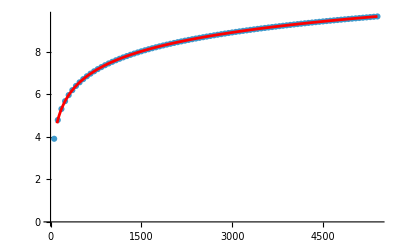

{b→-1.33492081006268632971910438573456641274668673052017614408586966816634731725133890364284306127858,c→1.27775363468805993675042251288794658373727036628213889679935793680333867876158804412335096200097}

```mathematica
(*For equal spaced puncture locations*)
Module[{table,tabelSubset,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[2]]]},{elt,TestTable3}];
tableSubset=Select[table,#[[1]]>5000&];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[tableSubset,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,5400},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];
]
```

```mathematica
{Lvals,v3}=Transpose[TestTable3];
   v4=TestTable4[[All,2]];
ratio=Transpose[{Lvals,v4/v3}];
ratioLog={#1,Log[#2]}&@@@ratio;
```

```mathematica
tableSubset=Select[ratioLog,#[[1]]>2000&];
```

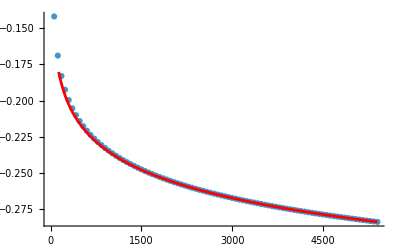

{b→-0.04274212811371347467979002453362444416756929529604983961073093349531944851636399272604190209919,c→-0.028028831704148872719261219500391289389153828298936003382224308201367069374193121125512085213423}

```mathematica
(*The ratio of equal spaced puncture locations and where one length equals zero*)
Module[{table,tableSubset,fit,P1,P2,Lvals,v3,v4,ratio,ratioLog},
{Lvals,v3}=Transpose[TestTable3];
   v4=TestTable4[[All,2]];
ratio=Transpose[{Lvals,v4/v3}];
ratioLog={#1,Log[#2]}&@@@ratio;
tableSubset=Select[ratioLog,#[[1]]>5000&];
P1=ListPlot[ratioLog,PlotRange->All];
fit=FindFit[tableSubset,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,5400},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];]
```

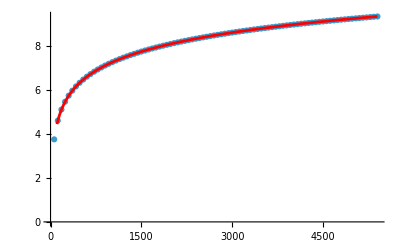

{b→-1.37766293817639980439889441026819085691425602581622598369660060166166676576770289636888496337777,c→1.24972480298391106403116129338755529434811653798320289341713362860197160938739492299783887678755}

```mathematica
(*This is for l1,l2,l3=(0,L/4,L/4)*)
Module[{table,tableSubset,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[2]]]},{elt,TestTable4}];
tableSubset=Select[table,#[[1]]>5000&];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[tableSubset,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,5400},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];]
```

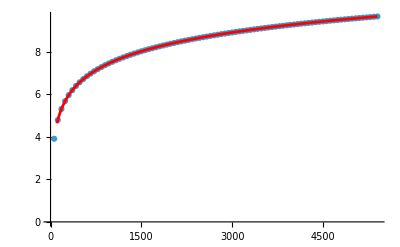

{b→-1.33475030064774644564528786892666355469846646584041807261626395336425222355770183561418056519593,c→1.27773340055963303035465490136102084774791281019523530981913115954910975849107060941195386757638}

```mathematica
Module[{table,tableSubset,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[2]]]},{elt,TestTable3}];
tableSubset=Select[table,#[[1]]>2000&];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[tableSubset,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,5400},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];]
```

```mathematica
Module[{table,tabelSubset,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[2]]]},{elt,TestTable3}];
tableSubset=Select[table,#[[1]]>4500&];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[tableSubset,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,5400},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];]
```

-Graphics-

{b→-1.3349064614770919065878022763685349387407954100710961138291610768886497269084500911528448372261,c→1.27775195784587929693996721532355505582465096462707531555766018874420654547846666764331066676938}

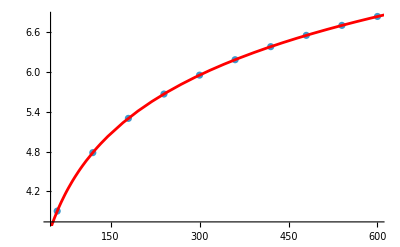

{b→-1.319243655334316339650671701416332312225802917972872766602902537006798915856099215030350782303084547,c→1.275218661464714575477676727758706422204162459023174408590789883029945009421058939199353692924372975}

```mathematica
(*{L,DetPrime[L,L/10,L/10]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[2]]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,1200},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];
]
```

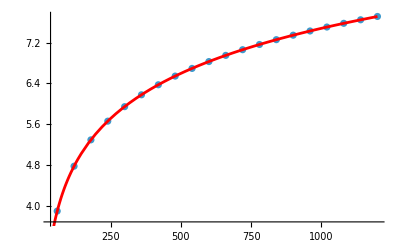

{b→-1.33593108255922581179389103923774974573359583706093052080234874660002064984333844018612789619349624,c→1.276013156666765259568761360596916263575093675349617499865180348910805943484237130998535478920631373}

```mathematica
(*{L,DetPrime[L,L/10,L/5]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[3]]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,1200},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];
]
```

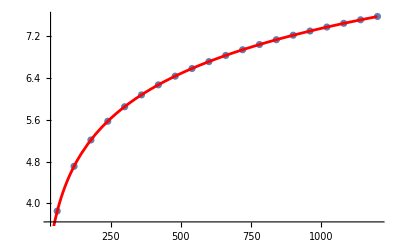

{b→-1.255316479389544174888300141418221145207719000144480150788325262719541885795481393258873072302183285,c→1.246496874684631932328950868802353376046221458235774919513721516132933563930955854594773355605488284}

```mathematica
(*{L,DetPrime[L,L/4-1,L/4-1]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[4]]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,1200},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];
]
```

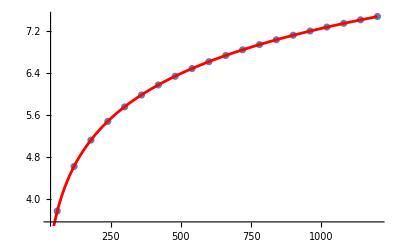

{b→-1.33900960841649708881755258304139696837131402589826984948023894157727427197726337465262122297032182,c→1.244045715212427792874040912402832983423732704715943485831504205896648118479423634110281887920022317}

```mathematica
(*{L,DetPrime[L,L/4,L/4]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[5]]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,1200},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];
]
```

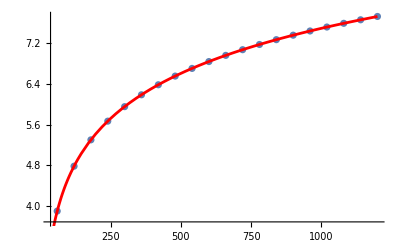

{b→-1.323995191816807802950796092413990689227335705276249125934866174271952537885206979405548581491438478,c→1.276123389706873296812889137216068844621171028631737104057288387605150142565370867441467324279977806}

```mathematica
(*{L,DetPrime[L,L/6,L/6]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],Log[elt[[6]]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,1200},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];
]
```

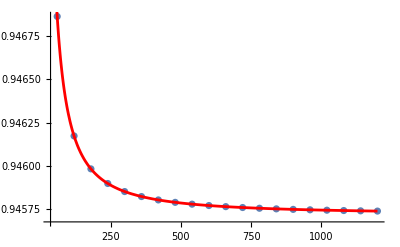

{a→0.945719318499014019207389622735965020703905050560034317360600405542326189656420481350218830565174132,b→0.266809487621357068220556674711002991654186089690292077325892257327271331219800357761314767843211555,c→1.33217433671771907207186448900852954509380991030071161007736404939525882922320766813304122262013148}

```mathematica
(*{L,DetPrime[L,L/10,L/10]/DetPrime[L,L/10,L/5]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],elt[[2]]/elt[[3]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,a+b/L^c,{a,b,c},L];
P2=Plot[a+b/L^c/.fit,{L,10,1200},PlotStyle->Red,PlotRange->All];
Print[Show[P1,P2]];
(*Print[ListLogPlot[Table[{elt[[1]],(elt[[2]]/elt[[3]]-a)/b/.fit},{elt,TestTable}]]];*)
Return[fit,Module];
]
```

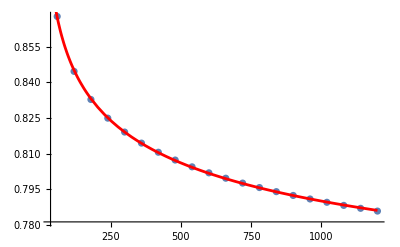

{a→0.647827588357148849780183154012376118057014031936333828849056942141967036625289945876716742441926183,b→0.412598949426550857313098358971654319496824047537484047992373587567073571198544345600773065634759841,c→0.154195476741352836753647228453037077482487319554812176194037508551943088199494426702901333588279863}

```mathematica
(*{L,DetPrime[L,L/4,L/4]/DetPrime[L,L/6,L/6]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],elt[[5]]/elt[[6]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,a+b/L^c,{a,b,c},L];
P2=Plot[a+b/L^c/.fit,{L,10,1200},PlotStyle->Red,PlotRange->All];
Print[Show[P1,P2]];
(*Print[ListLogPlot[Table[{elt[[1]],(elt[[2]]/elt[[3]]-a)/b/.fit},{elt,TestTable}]]];*)
Return[fit,Module];
]
```

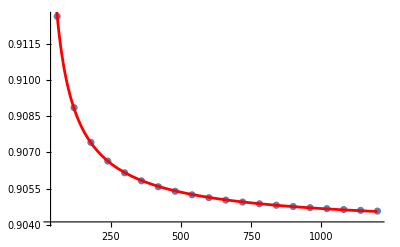

{a→0.903782058605274482593395459287765012241832547865740567942794197538949791753633414943670101996644553,b→0.250204512863610412523837658582977948126810153730301290178830671273430635643378303697895408418980654,c→0.816130766993602630028063941717978279035550407341211477794814780160641174388634325021072341647608106}

```mathematica
(*{L,DetPrime[L,L/4,L/4]/DetPrime[L,L/4-1,L/4-1]}*)
Module[{table,fit,P1,P2},
table=Table[{elt[[1]],elt[[5]]/elt[[4]]},{elt,TestTable}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,a+b/L^c,{a,b,c},L];
P2=Plot[a+b/L^c/.fit,{L,10,1200},PlotStyle->Red,PlotRange->All];
Print[Show[P1,P2]];
(*Print[ListLogPlot[Table[{elt[[1]],(elt[[2]]/elt[[3]]-a)/b/.fit},{elt,TestTable}]]];*)
Return[fit,Module];
]
```

```mathematica
SimpleTest2[L_]:=Module[{storedMat,storedMats,dets},
storedMat=DirectMatN[L,prec];
storedMats=Table[DirectRedTracedMat[L,L/4-n,L/4-n,storedMat],{n,{0,1,2,4,6,8,10,12,14}}];
AppendTo[storedMats,DirectRedTracedMat[L,L/4-L/60,L/4-L/60,storedMat]];
dets=Table[Det[stored]/(L/2),{stored,storedMats}];
Print[L];
Return[{L,dets},Module];
]
```

```mathematica
TestTable2=Table[SimpleTest2[L],{L,60,1200,60}]
```

60

120

180

240

300

360

420

480

540

600

660

720

780

840

900

960

1020

1080

1140

1200

{{60,{{43.0141623840581952413380919765595818488450896603408369097698343858869833800830964115452988351171459,47.132559991623368303150230505050675648742427238935754372320823726990953651244699630745788296335075,48.245323398386171348793253760476555632568367171019766802916848547504647227796575095690059075347501,49.4203075873573614848759066046663010648783764443933726255440202718062991175191368394729706382805654,49.4059922341169238664600470535933737633420517973136740594199494131198260472365713369442895990379589,47.8773969379947207950395920657163818159071006857485943246587574209370582903588813782162929422666307,44.2285612087229664771382837376041447783995626379654718599559513169551683913031142029758890537637192,37.2428913704065101349121889864240404255970341105525029207625452513562761109998220628875848818102581,23.1617659341558554512679532488924073705260733062458508208236284754751465972277255740625894133637025,47.132559991623368303150230505050675648742427238935754372320823726990953651244699630745788296335075}}},{120,{{101.091493447338352825250811979233363260345410041323058427811245871481472966269146870080505436970445,111.230435733299882982004968993464655499133980773064750212098919221832340327223655835555676112059926,113.588842605656361134838803019561786965117609244322740436241164874445350198213770627554445532399007,116.398062597914531241812471084874962516444057301602491969189895951643714083983500018327052486848673,118.212528432642980213644516997938981208979612101066416022356014056027368611617196176989810742431056,119.315377094784378671474538796603919589537028032575568760568590461083151769895530200348296535165919,119.698675304222771779251510873919915496426196105955486543755347687768810668154725072333688734452601,119.281478745866770464287654510460591940730380817062252745627496106892019596019308417766477567180336,117.945501368026804255026067814091550378093502395917269872573270586858702361785158829437222318866956,113.588842605656361134838803019561786965117609244322740436241164874445350198213770627554445532399007}}},{180,{{167.147080547286338251113979627739420279603949453987316217308492615680325026744888615163538997839492,184.202498166182510236920612389242079566368600179759279606579318868927274121985104501757983374158632,187.953382505207789209241497024117928168716669270056167195245632607107293473896989170314176149034808,192.247690930514185380767467941488103710282911099514467325752233215775007134253619654748631582534647,195.144740633243275835172034105984650191936696502464051664023921828118730851072140244983906647085651,197.33088251391333435290825191279644807904599915076248525791443525119625093252518795063266465976423,198.96389589378892157666775129720532588757993662384310113634059243134500820271929543679654723707992,200.074297780711002061323210571376951940703509565834681940901685654919769129772458909895697093836016,200.646850310492834541487314464979273484734742399353219345344221761921247712107313785964102700966222,190.374864917382870322834301168405935875216921580931808701951336843004990647457326220279561480620387}}},{240,{{239.004989395219738996947264878237300196543506199563878897263994806651684657224431776661725996962621,263.617070714785234421850751142620813880798614292189936045422737156517727936323992276010283322159923,268.888338985039031489243282369834169042838812347729738181588077130752438738196135909489942228294681,274.743585259870777489838341609756016428682775315323408863418352481559588788740879510674493353301322,278.640809629295453793910309269144554446923958769074423314865601978415013126034355938442219066795036,281.667445796954131603300073130173809453964414805812805284805148232844979775533814315135411360512013,284.123051671869768996832246513126016686867630528335897345368117511436873670207689888239208452886845,286.113145902007896810798260317728353773902803209756234976018505793014865880854217552110751858833059,287.673182877068569327997027090114543708930378611499736171598598393541406757468453426995858293484321,274.743585259870777489838341609756016428682775315323408863418352481559588788740879510674493353301322}}},{300,{{315.518799418255383667894422300820331255257708926478139238503827811202219588149419631296632912057015,348.196283094908762030300487197548092037729188880507257219397044409356249955757883906195221732213197,355.092476555147552200402845407622728210889269253238513352479264486947769056035911045297248154497,362.599063169469290988869571333482007877600733850046623729846365637969399629928998648871756018651151,367.507499897224252593871048857865512102743016584190346779509864394948648156215714892583375435521207,371.319236267880730452850506456480628000301044902699630345629925177409740561394788794673937260328191,374.473191429876144353361745531747409451864369571465037768593363636916922655789011116614430790412911,377.143175853939784902343785859318623812141975978662554639144067073659346778646895351920367121962028,379.405972838184546894709249417223569526798679026998617789433667035054941002418305907689701879835828,365.239191911172207252190135544562260421288412697569479754436763141042211761191216149423457086982262}}},{360,{{395.963904792912443390932294874077695794847486980944027220854606150268614964722626961051851720754216,437.133822172449331581554614035418754471811528766010147367967851098788108410716349048473431230920412,445.743164783761436022816455378976340059705497633873178503275875309333876307955843877651046812046112,454.985278745953963320088732433246082297224648296877868705532138575118261130972560647733585984823731,460.936893945577092655537541046499827606260282178110227653793439933883294992990048830295057980245253,465.528587200345083262760361053237209706606194077759073521651600177297707302998344466342795048216492,469.340565941678409997070153633701647992307699543596328188161532815640367507020611925920779279561742,472.613624903439121726579735653183109213694396567003774633926392158213861284271943485778843428166006,475.463228106612582552558805873018983850984503473489144912427130787136677579284692194979642371777381,460.936893945577092655537541046499827606260282178110227653793439933883294992990048830295057980245253}}},{420,{{479.834843598416227270950655036770249592874085887680986224519190960181106493336102137396083772723664,529.867858086609025626001203985296932694442550443958002443327496645149089351064979488854861030128208,540.26693674248536800403902087263975969906206443702625775264217385545711469987024862275372900476658,551.320533549053143079891608896509062568054221077002872991309128201724226471586324718411051967918204,558.351755636074518248135515945509616692561110460292187772461898585875931616711095346808268655520697,563.735178969518465208461063054792042212902717979130757422573178700192066960652888166344406166506778,568.195467249675891150355439415454724588480804773347938393580854029128931326384715314023891286611489,572.04072385768222657506548015449566937065553860356870076091722909945726936327228721194143646090227,575.424362865819417721057786671695151183044248695453590108159048144210806572823943113669480897026851,561.188806439712406854875512770771920252032315974486266721248249052999267389621902900009962418164391}}},{480,{{566.756131408111916358322968339832783798489685681644951550944732685363834419203412965435998169136258,625.981357880989160076717821240687257950304295228730614820989807734726707373310760158276248001429736,638.238088002991707439311369795884559293075815746315088996849303450262655192178804362076433919453855,651.171734556324519961062866439581219457516413013184524945773147259860207281480733884588799641217995,659.31876973033921774743649101858590843614208506165793814703731720410684547863281539406811641679189,665.511840343851607043381369079309630683807255395204920675484616430540946090620215766883598102402073,670.623587806071562690510015125779786312182692238160254268985040905090553129498071779864215183213674,675.030361613219284352488728560492305229633786036806014336979550917149028704261468592438444014715533,678.92352481283182513201653552400480960588089084576190563859554544091950890571407321573238120838634,665.511840343851607043381369079309630683807255395204920675484616430540946090620215766883598102402073}}},{540,{{656.436325856838946666543811303013917042240054998992872555591500620959560052546832606556251478810137,725.150814424792588900197928705609492616903100009997249203561294519978729665897856774933682238913258,739.326398696457797978998352648248090490405488567216400518628642832539648418025214593250724096068411,754.202442001208772642015179596955567457525226749307966646099385482228004076250686026712225948696821,763.499865402180145327647220574120078936599113443863364111097879738135644072554169751693218799933312,770.522567325630437965959413035307982342416130095521408004568980557405285380579540150083291837571656,776.294728959550673188485503658286404342651625536272304108077814432055064497322372949094552343752436,781.262131579226171855747763725637452933221414033711600520382315707788695100631548798284945547019622,785.65440923399265274215551999856545096903523702865063984943234819003679077701999658331488057527743,773.529790324218343976232278862727587362392855312916135077789702020363617635039999649753188464405089}}},{600,{{748.641755395412582094334212113792709203577078881025736758988052699241250964086065186755481444717552,827.116959737047385319372399942776589481426803955077837054567195042404712269355497908780799853198031,843.267242217797929594999197345897870864958391875224063331518252425683823949794683937160267567800064,860.142839201159998624105300374971818329720800353726640860885527468256288193796217279820937179054738,870.6232438485355666728781945933944082172082275338614544980047971996424317113423086947069358438931,878.49593938239785670357237693471420329900453130597305353550946645822695624850318854632972524965478,884.940129090399810559009678264166567414610353451134261200833219420065461173569990366862007510701955,890.47230646473867419814136750474774069870738130270855266856326482643085579086847731501947223120602,895.360852691908198761455700100051052049107558458687510933980534561998590527964887769614591261222631,884.940129090399810559009678264166567414610353451134261200833219420065461173569990366862007510701955}}},{660,{{843.180323307719939554608848469091005593876832780686664203548388217571644285441693079586417766373927,931.666727203635801436363285649108798692535710537370861051036231595658480146057435266750725475674602,949.843167326481264266162687911972554743722212412506388451055325342634966491224601645583241399775357,968.77111836554132126691490754401791516759521173692681170932170674801953312311234023193189801137739,980.46512896511083764278518427316462460350179517330657675886970696825354813574183367569976679385424,989.207831523760939079738299579466459390239176387582987530522414793821306697611913660029424618969755,996.33680825761274726368987139598007951780086858175161121157869655385465145174329704012524841962539,1002.44056923557675720405699349384536755993995029893715242297544694006938642489401293663965088775334,1007.82679342982174577637926010613865058110261999929718040613940362137423816320276747350728949925689,999.493487549417065611601970125379594953938037532965745428868383255607943888567633633332794569702767}}},{720,{{939.890939597622762987219113268505401827768097018015531999716539096353124583352882964348193921860552,1038.62149053678330031560961547067077850261136071000287107829143582470497729710404513729512171825969,1058.87188730375980960865731508554219352820904305128389410773892192263137315000108723115023985773074,1079.90129885475544998280087306860263452110860435507813524410721649800882389808698227850015482491992,1092.83770822011144779621040178440868972823145681509651795871010242652423326764134688784874773317798,1102.4697749059219784458824221360132059802859604744519535508127336232235945621409561503367740740347,1110.29667716266471339309726067261388655993378694896394599105841143489162423213997447324620608358587,1116.98023554246211333643082834011061588366038584421928576618371856453183210540449080663974046316188,1122.86801126306603228935387150273406024364171664456825616417261171684169061589680766138903844008615,1116.98023554246211333643082834011061588366038584421928576618371856453183210540449080663974046316188}}},{780,{{1038.63631066129918803999570226792900417370850336999680456809954143871038585713226141952685696432253,1147.82904444280835595846387089695956740508898521683429517374266422609092043436980689381579244169216,1170.19808997188252690563578332730340912841226501708290567474751533892223637965992066423541508782735,1193.37490239433351839377107233214879061427835776534581348649483160634092056883347198464573540004736,1207.58084026573464410422229603666376117007372213112186266477619291816467023504079161905878211790147,1218.12085755796940563294551640901385494160748192193835066398059088114479199680236358695285836921992,1226.65880555475188915705029788520275775185424596516478695598036612793779027190732348820794056524807,1233.93108189017559574812031150589342768965034036270303019969227021924775525258684849844737865059383,1240.32572633957910561551697647317171287679034285713030534713372452881669985969734972867945559023279,1237.22130726418081115500597414280868456254820013969236894224014125554023088516725542470362146848881}}},{840,{{1139.29783951307292909262507260578845901105573037571502260912046767497643308886491663983713990122004,1259.15793550223460690535123527203013405229641651951555109325463590774125175659551977275968181975712,1283.68764806917866795766129640060688783746527167602608344360080228311610338475902954688150806506388,1309.05505978323667000646828232848036396122428324185337752843181009884000581397749399813228589995037,1324.55615996959865530336986963299000079365062621936735570866607178916224031243953515366643848623363,1336.02192067797450602649091222646267410401465251211507603470981425760598916090373408469916243999692,1345.28380877755596777236472478148980229948365682819992849458141614867813199240764575986058636612094,1353.15403033035441120770224208544710908798169924086540083844266161238936030631321596343376596675412,1360.06169960173634425373942875580802649717469605868165649578149557108499649500773962149811982844858,1360.06169960173634425373942875580802649717469605868165649578149557108499649500773962149811982844858}}},{900,{{1241.77190998028792155425828589306872652094807650348335490223822930881202099812183098694033325247607,1372.49333326687083937244894666716535036619499405821659493333436606795882699080533359918184025325104,1399.22340280663487661606382928272159605435946700207126029125104833681589219540630738318940328621656,1426.82221489569380367686490898416866344995399670403553259768283250385189418760329667777061779362916,1443.64276863767060012040015612375570660193580314711541155178464602340716195290006490621716543286903,1456.05129188400901146176431395069970022181368605360495914173418356115512482597289706538782160718548,1466.04968328372925989039735300336611203274399966474164353600488624845351949175874888821385109507347,1474.52715017540920418374436038911985218667167323831507634927898991305631453464258378259971828842569,1481.95446996899521969774340811800321157554415320120424360803639754507575320775892001010743101342,1485.36572625537383441548583498720059824339351525340640377843200742081826760620962904753032009483047}}},{960,{{1345.96711085773561329109173880438663018176843123190575158799252165873659107311926521966482048463766,1487.73394691712279402962149279436074661237574993784285496710427714938902016649734201771814544867621,1516.70201536565790648143408740333788569510532785628423795482058023272042448735660502617977553671546,1546.57091472014971876816082400066747628946811208579306871060860828004153801139455979948620046505048,1564.73400701035283810840511771506680181165760318615597395686690290432194782384610752705878185271195,1578.10157754864486624636689933330163796568065098328786328603493054051372701037397806244410933626607,1588.84865539995916675616371029940459244579436760863043687952645622819069169750650068361133635267164,1597.94260281445740460729248487566850988168271070866879452753829303955631296396307518975937634600876,1605.89643787029471601620657373979654779605566757213298609593113183461882001795656197729481333686602,1613.01346630915326834598319688481385473076136048503788447716715496425152394593273116546022831637003}}},{1020,{{1451.80211766128011893512099865913782407608101122994002095071082107772885452364511483201080630976954,1604.78967308663616869743878602188672319647333322458699017197273329993164803318625998388471997829993,1636.03156519063365008826631985391074710901756507577358977133146781380450558112861425318999936730102,1668.20735969563731415165150197089504073978062403788079517261902099483054888341771836571190396067176,1687.73498880680167095524191936000122345456805532336151131941873493941459856699816469444552277928295,1702.07720380028324652663819353543360701785421164204675831777673937776471409106207735908164908191186,1713.5847539310224161411171383709200452758587200410047684806987090234992926958461478976485929662383,1723.30427142595779725537370406975720422276564313010593460277348027679887369101667427709031071317863,1731.79157936201164205146214257508818197372689006989373944365099489989405536931141613200016818602762,1742.89804974935926730020244314707789433439120376842256871004418703252281482236200423778132044681125}}},{1080,{{1559.20404625411049376702999897738329230368635086336450347696377826510790839604370524583918125687434,1723.5797681573203700827787183051055286163653792970800312786959743187821939591023506442882642549832,1757.12968393427419928648736745600202534663483194831932895467097100868569425037879979176481490637975,1791.64749982048143747527995281390596769457361930233860146220492543811637089344246319733697514370287,1812.56068157947887627832700499733276441702826345493186659243199283451825547450390475309375520455255,1827.89249885331663565173117099690781074481098183850572750657917324318827246785625515472099267935521,1840.17191022170161515806477394685930199978702925903561361608103560437462446944129929994093488987873,1850.52589574079245279336252938450624335702927519278743154452911141975293580164998638814950131034814,1859.55363363610914807134591253497242596010107428984443664438876568782742733724555525311619739100084,1874.92354444240794770653763723810136138726346784323323780864386497313815021577794355255987123299675}}},{1140,{{1668.10715258900165675573035485634984817722953899409517647523545281918124819306302663204042230040471,1844.03140512749765468031684602457620458231994924055968809407070112188523107976829394145659901062348,1879.92208215178874164994795352786411384534208782711684683196059559761823574765375247827883944560933,1916.81553115992706102316425557512830112164644800427556234858022928209321622145472207282157171111744,1939.13438985281040734133128928179808892041495552086201521338470423170747591206931331376800740502777,1955.47017467175582663521168594173734543922073850066773131759381301442937762639024767802882331199367,1968.53244961756400760739834981644024801097773126278633854782797217772128083943871532570850039098355,1979.52958492024875461786690221146595705505828801325834510910784050736836367680308752387817546282465,1989.10464958720408345253886049833283009986518899355695471320025384792931025938204918760544482591091,2009.00328490395408053609977098307256975551645751574701328393010352378774225954338869109579901429914}}},{1200,{{1778.45179124558014224233523810653798786863299516089755326291630075120655015125850648146968563395507,1966.07851794903065494801596438174207270924216615137303009057635389254100844009368729776211529587541,2004.3413695561770934561749570398428244093885941954512195914112859147141220342931825487872835953002,2043.64269175844525536274936310960179462169706771783957397349639100177328752775366870914034889113424,2067.38653951298965370679685890740916946452209730654819477728835272250798870838938828021204445961547,2084.74010851793339182154220604254691477877546337391816301656310922420639235156616916188201657993205,2098.59587819534892517691673024106456829901611677148459124536402209112333204472968295535281665832934,2110.24461763029477014300402726637275557777532948689590627945423667716874842751993728065119651793241,2120.37380778889087682867173236797951192515591415819847117925942164684772720979892373760658002212341,2145.05853184612948949361327644459573860585074354212682235444456111407552536459648943401911486422219}}}}

```mathematica
TestTable3=Table[SimpleTest2[L],{L,1200,1500,60}]
```

1200

1260

1320

1380

1440

1500

{{1200,{{1778.45179124558014224233523810653798786863299516089755326291630075120655015125850648146968563395507,1966.07851794903065494801596438174207270924216615137303009057635389254100844009368729776211529587541,2004.3413695561770934561749570398428244093885941954512195914112859147141220342931825487872835953002,2043.64269175844525536274936310960179462169706771783957397349639100177328752775366870914034889113424,2067.38653951298965370679685890740916946452209730654819477728835272250798870838938828021204445961547,2084.74010851793339182154220604254691477877546337391816301656310922420639235156616916188201657993205,2098.59587819534892517691673024106456829901611677148459124536402209112333204472968295535281665832934,2110.24461763029477014300402726637275557777532948689590627945423667716874842751993728065119651793241,2120.37380778889087682867173236797951192515591415819847117925942164684772720979892373760658002212341,2145.05853184612948949361327644459573860585074354212682235444456111407552536459648943401911486422219}}},{1260,{{1890.18357077668979911803779705868951791914425454496932106863700295704824584573972767019685946472702,2089.66086442516433345121850200356901218827292287929351501491396069350314670562467745184143878132416,2130.32609845117763947117070937582715192527408431953275834952044502877008106131860144301080632882805,2172.06628524205878035919735578271970206727558678754274506793949081494586125750779813506164256589657,2197.25369155174496052845593809112803851549495776645914407847226421225760128837145738892570926683963,2215.63835332290417175198698992477572612056400015494967756937354562598517341807181116038478462138017,2230.29789560420291094297872053121127243835101200275496681446875720742759317953090078714332093679083,2242.60646321854451380423707047932977912001084960614138489194233589036899595493748473402817383076907,2253.29645610924720042378692178552111830985605887612027331181175178629655794559106525043501363591665,2283.01738360012299759943196379485925008484739510446394520915767154306383107182919146075826383177424}}},{1320,{{2003.25266099494952662535771249548504762232492350568823544192862691099989060648650377370007921580064,2214.72325780374604112515401944153367977846279173109260404028667231724002047786903471982630336577735,2257.81997941180618451438168207614943165515997094093638832125365935582236747957387117531501255809464,2302.02888019038360319390658792610907185997037182277842986474435001654229782994782607553441898685454,2328.67773302292834815023960420233704677527928779557747133295405276095709324290152435223466685386954,2348.10632517258438983561055822340666076068804942733629762536409162436968721634576112619610629320483,2363.5795834280092383241260006741481045316467388716908106707994052852786463612289498369023983275571,2376.55597525363912299304642093516905841988186182127064347272376847658843615372496309837677082839455,2387.81331286696234666650040696236246111373639396277848205752702052751420253645512378626739258279534,2422.81388223109051819202921212036688625416766465274632349340871055673111620240200491708657257730845}}},{1380,{{2117.61321915098452061787187195136346685220830172616957944929702543497379635029164671101047944315459,2341.21493034661397770141186023114430279922758308161201389034534855607880751375309134511310399907089,2386.77123171144830866188015356089625074948685621512004814109096212630768161320080696161230996618238,2433.47764703308358266395978589214646908189444262073469651971107687598747850740114816439480794317719,2461.60520675172142556434149330270058869572564504970687750053535551426736634952100864275787864083939,2482.09012966968243942439970479347132593900203416694907333752319446256292531205170491297767731508269,2498.38673149390516677019727972099556740365334915598871931396886182256929617334356923789688933155077,2512.03872099277770974573633950483110298790305471259452868328962896260592892497585846034351240139135,2523.86980274640916168711988952422622845450284741329779688216498255938072243593715495788395679755683,2564.38727217815069624897876072626775410055700698275773887229318616672353451144778021539861470669683}}},{1440,{{2233.22291027852670756653112096677174903142756543401166626544573124144576082144856056181192070984895,2469.08900141053895782798246612003879992238865300914660665519440624771991964209287993014666802058552,2517.1320404477981148082629853034723384711761841357874526293830658603360342070695542282543444470353,2566.36380385773348183068017159041861691496946046847797543628187360237476879252246394400225732664028,2595.98675099112752512072983388610573131864654443267463834906266421207600107470076996707021743430029,2617.53999846957506624247767431778571680187149031074907841327873458350901615863746199206702026535775,2634.66927382614989898005158059697550996121228057328882386022145446362907453001595474973140567548406,2649.00441919338006423782948277171483337372419638805495108656653616941725812540593546494270091918342,2661.41549894309983467762266736148191502796315052265805054296693308183659373110652101409065054571908,2707.68137983752796553667364990768876877381009208377108607433448880392689275172978161553420140032466}}},{1500,{{2350.04250294675139837583877565043753081433528635307577594278588025758759861813962203737840058987869,2598.30202920565597779211048635910485879603327917168605126799671361042944904816171535649422656645499,2648.85809909253534367516770169003118701872762175679333970967015732091663873753376182015489528391043,2700.64214942016448111358732322716215401942266872588061833430322358097140445737627024303076173002736,2731.77662715140791181846120555286350563992836787602135467181295695166617418601548455438415432990444,2754.40981415595447889348141877767126074653655028862248927683266844124429273733271359208622264462713,2772.38081265471155879022373572745979431381400224459902014743739115471836785206590244376448634753555,2787.4064651360001533726344936415368208526968688313692158709137217292069943046951767529736870030472,2800.40365109316223475998473434536708222757057328315214834757748257518954127203751763039097985382704,2852.64409010077869043337890481368033249949775259309533548218303988487111275863312642800708498160708}}}}

```mathematica
TestTable4=Table[SimpleTest2[L],{L,1800,3000,300}]
```

1800

2100

2400

2700

3000

{{1800,{2951.09376707189609350429200163997326477421143478706437096800540293708199836837451720598759973307615,3263.12812905748249867003364008799886405295352167442987307734756956951440891357351990642330216694779,3326.61745788089024041961566064092284764741549831217557195867526267247106290408322159450298976793508,3391.53984254352748378977277336612962525042899086632108535691125002163368996575188704571977046333716,3430.45776317672358592921937289485459521682395731634445496880029690784092054442800817228872223916219,3458.65325349155414139227497575002496178475364461846190632083218183366388426838486052047621629941094,3480.95988014451478067669207397608067709079894579899904443201151484979573042282840616982183853092411,3499.54170928816189322382060495921511570152335908312259341620844440616869755840249788173553064998397,3515.55614036015017320984378843266715066601371073891828715441284333989854917982169089211526028499104,3600.8956829358188914490466692715248978204624123994774697915151117656195597611374170321956000517934}},{2100,{3577.80790825755325999088709291518752070082812689769124979395800836034536435450673708749950363544297,3956.3521353404515207799940547285977733799140734125333322919085198878130904856995195666966506978827,4033.3313358641904308895491349850641553357310337405017284566571170599896222077525125964630441022947,4111.96147277073522103864402582424391150754108035646403181639401762582203467157676820958295589562231,4159.00374559625439746375419928492147893506684122150517352632533159456508981986890495046883060925247,4193.00721539842241366287063285492221403846272584641924892400741311348620247945170623619342086609355,4219.84182728282390334200596928880410798627851797287063851644224191451087256961376664344745574745706,4242.13749661807776104316899656677664845694106862680593964826630189854718207996540107996635977417575,4261.30200651852164974610138574639342468121240728017947123812527226256306702839067910542116389829736,4384.7498956315351972281740768611654096317244908355635297075313202409218249379068446536848816776574}},{2400,{4227.3659585798654517147439870776029726867226371411428164867808974977959806274354265043892835337969,4674.85342133490064628253989315885929412806621603379273224696133354943616334380190006615642174877707,4765.81740571481717572979997722127239293642329074406630537603103099227039456142008420365853625980707,4858.66110297684559786898235096283141659258182358362514285528306743634792141992427601132476130654078,4914.13027571724060456308838950662312094157083690993470377571736108633293253587472294261935071103933,4954.15979427285922842478977889038852645428568936205665933354460264597073527619135261427608383827011,4985.69341430338185137513709526968950811420789224512119888419803346941096687339315595284671119755835,5011.84358233361713925115407975192180055079301196842580621473392812579572407862879431339321041450489,5034.27733413231865933411206299118002376099387966350411666356643751466800512862239575262676761605264,5200.43095155674109097676713074273357458579631212550669973826354798906842901179481037739794892857451}},{2700,{4897.58111123191846239434379312969982266580095012672180112632901655472586489621146512999856589089111,5416.21142113890905209442987657847786681441932349535203415473354362489501467556232074762910051661231,5521.60736125993301204667933305232904366519943118811308117767538069445470682773103781339528986558987,5629.12129882331758940784705958086058651574995984012302123209659406164752770268902992331635153205315,5693.29030114721978258147541579691164990953154360557475077187601576035690037111482405021646985938369,5739.54254080956092594826826876925650946378629632519396671715934134884136764821940202820275393810716,5775.9295021402814978486754526704000753733112540715920766118649031818033929281986469768035495968185,5806.06130564806742278013263616738203271387437105707569680998029307397860537659786800397640000888187,5831.87230958843919643027604941383501132636986493826974559011769942119709034026309640937217292317989,6044.99830221024052004152830911690498644800844742476126772806095312840608344894214805184692897711261}},{3000,{5586.70077460994019494578535631320338577755204656511036013244932748381167654811044721997861524867426,6178.48635030412808662121279829370265439980610501205267931873604939747197120748052808273607482365378,6298.72323020726783688285619257606785569622847555248106995824476511078843890417303832220803768509397,6421.32484927053477175045023054682469280696435395242148429815333867032845600490973938786458159856224,6494.44297656813221297048207596104074969180695301298550026333880834099179106176742882958962088068223,6547.09750922134466693533610611672498436318969084116188659953893672011647272161709928706939283280022,6588.47874313730506586583999213747461243192779697601571528739004044863385407821137177317038263098035,6622.70836622234106038972443725050196933259849944385331444769194388876161811653221011000376020600856,6651.99547471811220295846097271240078558633659084583764337908497728081644555240726799386185954032413,6916.08719222049594928528454082212424757527715452813432241499665790886443170351954858688712626802505}}}

```mathematica
TestTableFull=Join[TestTable2,TestTable3];
TestTableFull = Table[{elt[[1]],elt[[2,1]]},{elt,TestTableFull}];
TestTableFull=Join[TestTableFull,TestTable4]
```

{{60,{43.0141623840581952413380919765595818488450896603408369097698343858869833800830964115452988351171459,47.132559991623368303150230505050675648742427238935754372320823726990953651244699630745788296335075,48.245323398386171348793253760476555632568367171019766802916848547504647227796575095690059075347501,49.4203075873573614848759066046663010648783764443933726255440202718062991175191368394729706382805654,49.4059922341169238664600470535933737633420517973136740594199494131198260472365713369442895990379589,47.8773969379947207950395920657163818159071006857485943246587574209370582903588813782162929422666307,44.2285612087229664771382837376041447783995626379654718599559513169551683913031142029758890537637192,37.2428913704065101349121889864240404255970341105525029207625452513562761109998220628875848818102581,23.1617659341558554512679532488924073705260733062458508208236284754751465972277255740625894133637025,47.132559991623368303150230505050675648742427238935754372320823726990953651244699630745788296335075}},{120,{101.091493447338352825250811979233363260345410041323058427811245871481472966269146870080505436970445,111.230435733299882982004968993464655499133980773064750212098919221832340327223655835555676112059926,113.588842605656361134838803019561786965117609244322740436241164874445350198213770627554445532399007,116.398062597914531241812471084874962516444057301602491969189895951643714083983500018327052486848673,118.212528432642980213644516997938981208979612101066416022356014056027368611617196176989810742431056,119.315377094784378671474538796603919589537028032575568760568590461083151769895530200348296535165919,119.698675304222771779251510873919915496426196105955486543755347687768810668154725072333688734452601,119.281478745866770464287654510460591940730380817062252745627496106892019596019308417766477567180336,117.945501368026804255026067814091550378093502395917269872573270586858702361785158829437222318866956,113.588842605656361134838803019561786965117609244322740436241164874445350198213770627554445532399007}},{180,{167.147080547286338251113979627739420279603949453987316217308492615680325026744888615163538997839492,184.202498166182510236920612389242079566368600179759279606579318868927274121985104501757983374158632,187.953382505207789209241497024117928168716669270056167195245632607107293473896989170314176149034808,192.247690930514185380767467941488103710282911099514467325752233215775007134253619654748631582534647,195.144740633243275835172034105984650191936696502464051664023921828118730851072140244983906647085651,197.33088251391333435290825191279644807904599915076248525791443525119625093252518795063266465976423,198.96389589378892157666775129720532588757993662384310113634059243134500820271929543679654723707992,200.074297780711002061323210571376951940703509565834681940901685654919769129772458909895697093836016,200.646850310492834541487314464979273484734742399353219345344221761921247712107313785964102700966222,190.374864917382870322834301168405935875216921580931808701951336843004990647457326220279561480620387}},{240,{239.004989395219738996947264878237300196543506199563878897263994806651684657224431776661725996962621,263.617070714785234421850751142620813880798614292189936045422737156517727936323992276010283322159923,268.888338985039031489243282369834169042838812347729738181588077130752438738196135909489942228294681,274.743585259870777489838341609756016428682775315323408863418352481559588788740879510674493353301322,278.640809629295453793910309269144554446923958769074423314865601978415013126034355938442219066795036,281.667445796954131603300073130173809453964414805812805284805148232844979775533814315135411360512013,284.123051671869768996832246513126016686867630528335897345368117511436873670207689888239208452886845,286.113145902007896810798260317728353773902803209756234976018505793014865880854217552110751858833059,287.673182877068569327997027090114543708930378611499736171598598393541406757468453426995858293484321,274.743585259870777489838341609756016428682775315323408863418352481559588788740879510674493353301322}},{300,{315.518799418255383667894422300820331255257708926478139238503827811202219588149419631296632912057015,348.196283094908762030300487197548092037729188880507257219397044409356249955757883906195221732213197,355.092476555147552200402845407622728210889269253238513352479264486947769056035911045297248154497,362.599063169469290988869571333482007877600733850046623729846365637969399629928998648871756018651151,367.507499897224252593871048857865512102743016584190346779509864394948648156215714892583375435521207,371.319236267880730452850506456480628000301044902699630345629925177409740561394788794673937260328191,374.473191429876144353361745531747409451864369571465037768593363636916922655789011116614430790412911,377.143175853939784902343785859318623812141975978662554639144067073659346778646895351920367121962028,379.405972838184546894709249417223569526798679026998617789433667035054941002418305907689701879835828,365.239191911172207252190135544562260421288412697569479754436763141042211761191216149423457086982262}},{360,{395.963904792912443390932294874077695794847486980944027220854606150268614964722626961051851720754216,437.133822172449331581554614035418754471811528766010147367967851098788108410716349048473431230920412,445.743164783761436022816455378976340059705497633873178503275875309333876307955843877651046812046112,454.985278745953963320088732433246082297224648296877868705532138575118261130972560647733585984823731,460.936893945577092655537541046499827606260282178110227653793439933883294992990048830295057980245253,465.528587200345083262760361053237209706606194077759073521651600177297707302998344466342795048216492,469.340565941678409997070153633701647992307699543596328188161532815640367507020611925920779279561742,472.613624903439121726579735653183109213694396567003774633926392158213861284271943485778843428166006,475.463228106612582552558805873018983850984503473489144912427130787136677579284692194979642371777381,460.936893945577092655537541046499827606260282178110227653793439933883294992990048830295057980245253}},{420,{479.834843598416227270950655036770249592874085887680986224519190960181106493336102137396083772723664,529.867858086609025626001203985296932694442550443958002443327496645149089351064979488854861030128208,540.26693674248536800403902087263975969906206443702625775264217385545711469987024862275372900476658,551.320533549053143079891608896509062568054221077002872991309128201724226471586324718411051967918204,558.351755636074518248135515945509616692561110460292187772461898585875931616711095346808268655520697,563.735178969518465208461063054792042212902717979130757422573178700192066960652888166344406166506778,568.195467249675891150355439415454724588480804773347938393580854029128931326384715314023891286611489,572.04072385768222657506548015449566937065553860356870076091722909945726936327228721194143646090227,575.424362865819417721057786671695151183044248695453590108159048144210806572823943113669480897026851,561.188806439712406854875512770771920252032315974486266721248249052999267389621902900009962418164391}},{480,{566.756131408111916358322968339832783798489685681644951550944732685363834419203412965435998169136258,625.981357880989160076717821240687257950304295228730614820989807734726707373310760158276248001429736,638.238088002991707439311369795884559293075815746315088996849303450262655192178804362076433919453855,651.171734556324519961062866439581219457516413013184524945773147259860207281480733884588799641217995,659.31876973033921774743649101858590843614208506165793814703731720410684547863281539406811641679189,665.511840343851607043381369079309630683807255395204920675484616430540946090620215766883598102402073,670.623587806071562690510015125779786312182692238160254268985040905090553129498071779864215183213674,675.030361613219284352488728560492305229633786036806014336979550917149028704261468592438444014715533,678.92352481283182513201653552400480960588089084576190563859554544091950890571407321573238120838634,665.511840343851607043381369079309630683807255395204920675484616430540946090620215766883598102402073}},{540,{656.436325856838946666543811303013917042240054998992872555591500620959560052546832606556251478810137,725.150814424792588900197928705609492616903100009997249203561294519978729665897856774933682238913258,739.326398696457797978998352648248090490405488567216400518628642832539648418025214593250724096068411,754.202442001208772642015179596955567457525226749307966646099385482228004076250686026712225948696821,763.499865402180145327647220574120078936599113443863364111097879738135644072554169751693218799933312,770.522567325630437965959413035307982342416130095521408004568980557405285380579540150083291837571656,776.294728959550673188485503658286404342651625536272304108077814432055064497322372949094552343752436,781.262131579226171855747763725637452933221414033711600520382315707788695100631548798284945547019622,785.65440923399265274215551999856545096903523702865063984943234819003679077701999658331488057527743,773.529790324218343976232278862727587362392855312916135077789702020363617635039999649753188464405089}},{600,{748.641755395412582094334212113792709203577078881025736758988052699241250964086065186755481444717552,827.116959737047385319372399942776589481426803955077837054567195042404712269355497908780799853198031,843.267242217797929594999197345897870864958391875224063331518252425683823949794683937160267567800064,860.142839201159998624105300374971818329720800353726640860885527468256288193796217279820937179054738,870.6232438485355666728781945933944082172082275338614544980047971996424317113423086947069358438931,878.49593938239785670357237693471420329900453130597305353550946645822695624850318854632972524965478,884.940129090399810559009678264166567414610353451134261200833219420065461173569990366862007510701955,890.47230646473867419814136750474774069870738130270855266856326482643085579086847731501947223120602,895.360852691908198761455700100051052049107558458687510933980534561998590527964887769614591261222631,884.940129090399810559009678264166567414610353451134261200833219420065461173569990366862007510701955}},{660,{843.180323307719939554608848469091005593876832780686664203548388217571644285441693079586417766373927,931.666727203635801436363285649108798692535710537370861051036231595658480146057435266750725475674602,949.843167326481264266162687911972554743722212412506388451055325342634966491224601645583241399775357,968.77111836554132126691490754401791516759521173692681170932170674801953312311234023193189801137739,980.46512896511083764278518427316462460350179517330657675886970696825354813574183367569976679385424,989.207831523760939079738299579466459390239176387582987530522414793821306697611913660029424618969755,996.33680825761274726368987139598007951780086858175161121157869655385465145174329704012524841962539,1002.44056923557675720405699349384536755993995029893715242297544694006938642489401293663965088775334,1007.82679342982174577637926010613865058110261999929718040613940362137423816320276747350728949925689,999.493487549417065611601970125379594953938037532965745428868383255607943888567633633332794569702767}},{720,{939.890939597622762987219113268505401827768097018015531999716539096353124583352882964348193921860552,1038.62149053678330031560961547067077850261136071000287107829143582470497729710404513729512171825969,1058.87188730375980960865731508554219352820904305128389410773892192263137315000108723115023985773074,1079.90129885475544998280087306860263452110860435507813524410721649800882389808698227850015482491992,1092.83770822011144779621040178440868972823145681509651795871010242652423326764134688784874773317798,1102.4697749059219784458824221360132059802859604744519535508127336232235945621409561503367740740347,1110.29667716266471339309726067261388655993378694896394599105841143489162423213997447324620608358587,1116.98023554246211333643082834011061588366038584421928576618371856453183210540449080663974046316188,1122.86801126306603228935387150273406024364171664456825616417261171684169061589680766138903844008615,1116.98023554246211333643082834011061588366038584421928576618371856453183210540449080663974046316188}},{780,{1038.63631066129918803999570226792900417370850336999680456809954143871038585713226141952685696432253,1147.82904444280835595846387089695956740508898521683429517374266422609092043436980689381579244169216,1170.19808997188252690563578332730340912841226501708290567474751533892223637965992066423541508782735,1193.37490239433351839377107233214879061427835776534581348649483160634092056883347198464573540004736,1207.58084026573464410422229603666376117007372213112186266477619291816467023504079161905878211790147,1218.12085755796940563294551640901385494160748192193835066398059088114479199680236358695285836921992,1226.65880555475188915705029788520275775185424596516478695598036612793779027190732348820794056524807,1233.93108189017559574812031150589342768965034036270303019969227021924775525258684849844737865059383,1240.32572633957910561551697647317171287679034285713030534713372452881669985969734972867945559023279,1237.22130726418081115500597414280868456254820013969236894224014125554023088516725542470362146848881}},{840,{1139.29783951307292909262507260578845901105573037571502260912046767497643308886491663983713990122004,1259.15793550223460690535123527203013405229641651951555109325463590774125175659551977275968181975712,1283.68764806917866795766129640060688783746527167602608344360080228311610338475902954688150806506388,1309.05505978323667000646828232848036396122428324185337752843181009884000581397749399813228589995037,1324.55615996959865530336986963299000079365062621936735570866607178916224031243953515366643848623363,1336.02192067797450602649091222646267410401465251211507603470981425760598916090373408469916243999692,1345.28380877755596777236472478148980229948365682819992849458141614867813199240764575986058636612094,1353.15403033035441120770224208544710908798169924086540083844266161238936030631321596343376596675412,1360.06169960173634425373942875580802649717469605868165649578149557108499649500773962149811982844858,1360.06169960173634425373942875580802649717469605868165649578149557108499649500773962149811982844858}},{900,{1241.77190998028792155425828589306872652094807650348335490223822930881202099812183098694033325247607,1372.49333326687083937244894666716535036619499405821659493333436606795882699080533359918184025325104,1399.22340280663487661606382928272159605435946700207126029125104833681589219540630738318940328621656,1426.82221489569380367686490898416866344995399670403553259768283250385189418760329667777061779362916,1443.64276863767060012040015612375570660193580314711541155178464602340716195290006490621716543286903,1456.05129188400901146176431395069970022181368605360495914173418356115512482597289706538782160718548,1466.04968328372925989039735300336611203274399966474164353600488624845351949175874888821385109507347,1474.52715017540920418374436038911985218667167323831507634927898991305631453464258378259971828842569,1481.95446996899521969774340811800321157554415320120424360803639754507575320775892001010743101342,1485.36572625537383441548583498720059824339351525340640377843200742081826760620962904753032009483047}},{960,{1345.96711085773561329109173880438663018176843123190575158799252165873659107311926521966482048463766,1487.73394691712279402962149279436074661237574993784285496710427714938902016649734201771814544867621,1516.70201536565790648143408740333788569510532785628423795482058023272042448735660502617977553671546,1546.57091472014971876816082400066747628946811208579306871060860828004153801139455979948620046505048,1564.73400701035283810840511771506680181165760318615597395686690290432194782384610752705878185271195,1578.10157754864486624636689933330163796568065098328786328603493054051372701037397806244410933626607,1588.84865539995916675616371029940459244579436760863043687952645622819069169750650068361133635267164,1597.94260281445740460729248487566850988168271070866879452753829303955631296396307518975937634600876,1605.89643787029471601620657373979654779605566757213298609593113183461882001795656197729481333686602,1613.01346630915326834598319688481385473076136048503788447716715496425152394593273116546022831637003}},{1020,{1451.80211766128011893512099865913782407608101122994002095071082107772885452364511483201080630976954,1604.78967308663616869743878602188672319647333322458699017197273329993164803318625998388471997829993,1636.03156519063365008826631985391074710901756507577358977133146781380450558112861425318999936730102,1668.20735969563731415165150197089504073978062403788079517261902099483054888341771836571190396067176,1687.73498880680167095524191936000122345456805532336151131941873493941459856699816469444552277928295,1702.07720380028324652663819353543360701785421164204675831777673937776471409106207735908164908191186,1713.5847539310224161411171383709200452758587200410047684806987090234992926958461478976485929662383,1723.30427142595779725537370406975720422276564313010593460277348027679887369101667427709031071317863,1731.79157936201164205146214257508818197372689006989373944365099489989405536931141613200016818602762,1742.89804974935926730020244314707789433439120376842256871004418703252281482236200423778132044681125}},{1080,{1559.20404625411049376702999897738329230368635086336450347696377826510790839604370524583918125687434,1723.5797681573203700827787183051055286163653792970800312786959743187821939591023506442882642549832,1757.12968393427419928648736745600202534663483194831932895467097100868569425037879979176481490637975,1791.64749982048143747527995281390596769457361930233860146220492543811637089344246319733697514370287,1812.56068157947887627832700499733276441702826345493186659243199283451825547450390475309375520455255,1827.89249885331663565173117099690781074481098183850572750657917324318827246785625515472099267935521,1840.17191022170161515806477394685930199978702925903561361608103560437462446944129929994093488987873,1850.52589574079245279336252938450624335702927519278743154452911141975293580164998638814950131034814,1859.55363363610914807134591253497242596010107428984443664438876568782742733724555525311619739100084,1874.92354444240794770653763723810136138726346784323323780864386497313815021577794355255987123299675}},{1140,{1668.10715258900165675573035485634984817722953899409517647523545281918124819306302663204042230040471,1844.03140512749765468031684602457620458231994924055968809407070112188523107976829394145659901062348,1879.92208215178874164994795352786411384534208782711684683196059559761823574765375247827883944560933,1916.81553115992706102316425557512830112164644800427556234858022928209321622145472207282157171111744,1939.13438985281040734133128928179808892041495552086201521338470423170747591206931331376800740502777,1955.47017467175582663521168594173734543922073850066773131759381301442937762639024767802882331199367,1968.53244961756400760739834981644024801097773126278633854782797217772128083943871532570850039098355,1979.52958492024875461786690221146595705505828801325834510910784050736836367680308752387817546282465,1989.10464958720408345253886049833283009986518899355695471320025384792931025938204918760544482591091,2009.00328490395408053609977098307256975551645751574701328393010352378774225954338869109579901429914}},{1200,{1778.45179124558014224233523810653798786863299516089755326291630075120655015125850648146968563395507,1966.07851794903065494801596438174207270924216615137303009057635389254100844009368729776211529587541,2004.3413695561770934561749570398428244093885941954512195914112859147141220342931825487872835953002,2043.64269175844525536274936310960179462169706771783957397349639100177328752775366870914034889113424,2067.38653951298965370679685890740916946452209730654819477728835272250798870838938828021204445961547,2084.74010851793339182154220604254691477877546337391816301656310922420639235156616916188201657993205,2098.59587819534892517691673024106456829901611677148459124536402209112333204472968295535281665832934,2110.24461763029477014300402726637275557777532948689590627945423667716874842751993728065119651793241,2120.37380778889087682867173236797951192515591415819847117925942164684772720979892373760658002212341,2145.05853184612948949361327644459573860585074354212682235444456111407552536459648943401911486422219}},{1200,{1778.45179124558014224233523810653798786863299516089755326291630075120655015125850648146968563395507,1966.07851794903065494801596438174207270924216615137303009057635389254100844009368729776211529587541,2004.3413695561770934561749570398428244093885941954512195914112859147141220342931825487872835953002,2043.64269175844525536274936310960179462169706771783957397349639100177328752775366870914034889113424,2067.38653951298965370679685890740916946452209730654819477728835272250798870838938828021204445961547,2084.74010851793339182154220604254691477877546337391816301656310922420639235156616916188201657993205,2098.59587819534892517691673024106456829901611677148459124536402209112333204472968295535281665832934,2110.24461763029477014300402726637275557777532948689590627945423667716874842751993728065119651793241,2120.37380778889087682867173236797951192515591415819847117925942164684772720979892373760658002212341,2145.05853184612948949361327644459573860585074354212682235444456111407552536459648943401911486422219}},{1260,{1890.18357077668979911803779705868951791914425454496932106863700295704824584573972767019685946472702,2089.66086442516433345121850200356901218827292287929351501491396069350314670562467745184143878132416,2130.32609845117763947117070937582715192527408431953275834952044502877008106131860144301080632882805,2172.06628524205878035919735578271970206727558678754274506793949081494586125750779813506164256589657,2197.25369155174496052845593809112803851549495776645914407847226421225760128837145738892570926683963,2215.63835332290417175198698992477572612056400015494967756937354562598517341807181116038478462138017,2230.29789560420291094297872053121127243835101200275496681446875720742759317953090078714332093679083,2242.60646321854451380423707047932977912001084960614138489194233589036899595493748473402817383076907,2253.29645610924720042378692178552111830985605887612027331181175178629655794559106525043501363591665,2283.01738360012299759943196379485925008484739510446394520915767154306383107182919146075826383177424}},{1320,{2003.25266099494952662535771249548504762232492350568823544192862691099989060648650377370007921580064,2214.72325780374604112515401944153367977846279173109260404028667231724002047786903471982630336577735,2257.81997941180618451438168207614943165515997094093638832125365935582236747957387117531501255809464,2302.02888019038360319390658792610907185997037182277842986474435001654229782994782607553441898685454,2328.67773302292834815023960420233704677527928779557747133295405276095709324290152435223466685386954,2348.10632517258438983561055822340666076068804942733629762536409162436968721634576112619610629320483,2363.5795834280092383241260006741481045316467388716908106707994052852786463612289498369023983275571,2376.55597525363912299304642093516905841988186182127064347272376847658843615372496309837677082839455,2387.81331286696234666650040696236246111373639396277848205752702052751420253645512378626739258279534,2422.81388223109051819202921212036688625416766465274632349340871055673111620240200491708657257730845}},{1380,{2117.61321915098452061787187195136346685220830172616957944929702543497379635029164671101047944315459,2341.21493034661397770141186023114430279922758308161201389034534855607880751375309134511310399907089,2386.77123171144830866188015356089625074948685621512004814109096212630768161320080696161230996618238,2433.47764703308358266395978589214646908189444262073469651971107687598747850740114816439480794317719,2461.60520675172142556434149330270058869572564504970687750053535551426736634952100864275787864083939,2482.09012966968243942439970479347132593900203416694907333752319446256292531205170491297767731508269,2498.38673149390516677019727972099556740365334915598871931396886182256929617334356923789688933155077,2512.03872099277770974573633950483110298790305471259452868328962896260592892497585846034351240139135,2523.86980274640916168711988952422622845450284741329779688216498255938072243593715495788395679755683,2564.38727217815069624897876072626775410055700698275773887229318616672353451144778021539861470669683}},{1440,{2233.22291027852670756653112096677174903142756543401166626544573124144576082144856056181192070984895,2469.08900141053895782798246612003879992238865300914660665519440624771991964209287993014666802058552,2517.1320404477981148082629853034723384711761841357874526293830658603360342070695542282543444470353,2566.36380385773348183068017159041861691496946046847797543628187360237476879252246394400225732664028,2595.98675099112752512072983388610573131864654443267463834906266421207600107470076996707021743430029,2617.53999846957506624247767431778571680187149031074907841327873458350901615863746199206702026535775,2634.66927382614989898005158059697550996121228057328882386022145446362907453001595474973140567548406,2649.00441919338006423782948277171483337372419638805495108656653616941725812540593546494270091918342,2661.41549894309983467762266736148191502796315052265805054296693308183659373110652101409065054571908,2707.68137983752796553667364990768876877381009208377108607433448880392689275172978161553420140032466}},{1500,{2350.04250294675139837583877565043753081433528635307577594278588025758759861813962203737840058987869,2598.30202920565597779211048635910485879603327917168605126799671361042944904816171535649422656645499,2648.85809909253534367516770169003118701872762175679333970967015732091663873753376182015489528391043,2700.64214942016448111358732322716215401942266872588061833430322358097140445737627024303076173002736,2731.77662715140791181846120555286350563992836787602135467181295695166617418601548455438415432990444,2754.40981415595447889348141877767126074653655028862248927683266844124429273733271359208622264462713,2772.38081265471155879022373572745979431381400224459902014743739115471836785206590244376448634753555,2787.4064651360001533726344936415368208526968688313692158709137217292069943046951767529736870030472,2800.40365109316223475998473434536708222757057328315214834757748257518954127203751763039097985382704,2852.64409010077869043337890481368033249949775259309533548218303988487111275863312642800708498160708}},{1800,{2951.09376707189609350429200163997326477421143478706437096800540293708199836837451720598759973307615,3263.12812905748249867003364008799886405295352167442987307734756956951440891357351990642330216694779,3326.61745788089024041961566064092284764741549831217557195867526267247106290408322159450298976793508,3391.53984254352748378977277336612962525042899086632108535691125002163368996575188704571977046333716,3430.45776317672358592921937289485459521682395731634445496880029690784092054442800817228872223916219,3458.65325349155414139227497575002496178475364461846190632083218183366388426838486052047621629941094,3480.95988014451478067669207397608067709079894579899904443201151484979573042282840616982183853092411,3499.54170928816189322382060495921511570152335908312259341620844440616869755840249788173553064998397,3515.55614036015017320984378843266715066601371073891828715441284333989854917982169089211526028499104,3600.8956829358188914490466692715248978204624123994774697915151117656195597611374170321956000517934}},{2100,{3577.80790825755325999088709291518752070082812689769124979395800836034536435450673708749950363544297,3956.3521353404515207799940547285977733799140734125333322919085198878130904856995195666966506978827,4033.3313358641904308895491349850641553357310337405017284566571170599896222077525125964630441022947,4111.96147277073522103864402582424391150754108035646403181639401762582203467157676820958295589562231,4159.00374559625439746375419928492147893506684122150517352632533159456508981986890495046883060925247,4193.00721539842241366287063285492221403846272584641924892400741311348620247945170623619342086609355,4219.84182728282390334200596928880410798627851797287063851644224191451087256961376664344745574745706,4242.13749661807776104316899656677664845694106862680593964826630189854718207996540107996635977417575,4261.30200651852164974610138574639342468121240728017947123812527226256306702839067910542116389829736,4384.7498956315351972281740768611654096317244908355635297075313202409218249379068446536848816776574}},{2400,{4227.3659585798654517147439870776029726867226371411428164867808974977959806274354265043892835337969,4674.85342133490064628253989315885929412806621603379273224696133354943616334380190006615642174877707,4765.81740571481717572979997722127239293642329074406630537603103099227039456142008420365853625980707,4858.66110297684559786898235096283141659258182358362514285528306743634792141992427601132476130654078,4914.13027571724060456308838950662312094157083690993470377571736108633293253587472294261935071103933,4954.15979427285922842478977889038852645428568936205665933354460264597073527619135261427608383827011,4985.69341430338185137513709526968950811420789224512119888419803346941096687339315595284671119755835,5011.84358233361713925115407975192180055079301196842580621473392812579572407862879431339321041450489,5034.27733413231865933411206299118002376099387966350411666356643751466800512862239575262676761605264,5200.43095155674109097676713074273357458579631212550669973826354798906842901179481037739794892857451}},{2700,{4897.58111123191846239434379312969982266580095012672180112632901655472586489621146512999856589089111,5416.21142113890905209442987657847786681441932349535203415473354362489501467556232074762910051661231,5521.60736125993301204667933305232904366519943118811308117767538069445470682773103781339528986558987,5629.12129882331758940784705958086058651574995984012302123209659406164752770268902992331635153205315,5693.29030114721978258147541579691164990953154360557475077187601576035690037111482405021646985938369,5739.54254080956092594826826876925650946378629632519396671715934134884136764821940202820275393810716,5775.9295021402814978486754526704000753733112540715920766118649031818033929281986469768035495968185,5806.06130564806742278013263616738203271387437105707569680998029307397860537659786800397640000888187,5831.87230958843919643027604941383501132636986493826974559011769942119709034026309640937217292317989,6044.99830221024052004152830911690498644800844742476126772806095312840608344894214805184692897711261}},{3000,{5586.70077460994019494578535631320338577755204656511036013244932748381167654811044721997861524867426,6178.48635030412808662121279829370265439980610501205267931873604939747197120748052808273607482365378,6298.72323020726783688285619257606785569622847555248106995824476511078843890417303832220803768509397,6421.32484927053477175045023054682469280696435395242148429815333867032845600490973938786458159856224,6494.44297656813221297048207596104074969180695301298550026333880834099179106176742882958962088068223,6547.09750922134466693533610611672498436318969084116188659953893672011647272161709928706939283280022,6588.47874313730506586583999213747461243192779697601571528739004044863385407821137177317038263098035,6622.70836622234106038972443725050196933259849944385331444769194388876161811653221011000376020600856,6651.99547471811220295846097271240078558633659084583764337908497728081644555240726799386185954032413,6916.08719222049594928528454082212424757527715452813432241499665790886443170351954858688712626802505}}}

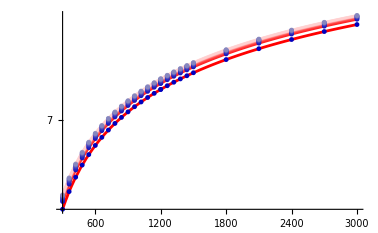

{{b[1]→-1.366805440092174926352767812155097067775253372601927044546523245982727973793859505515600264484851521,c[1]→1.24829461830754884804876701618781904150960964756448122519608791216143708139492845945341363241011691},{b[2]→-1.272706677576836577720158565341262334556129637501512772092286875053534760736099235973737006756000071,c[2]→1.249155356912619479846380740259845827460717877525118043728175623663619176521552788230966037424998146},{b[3]→-1.252631906789276049066065319048821068401635362893755292022176117933617638989017532826654951652113462,c[3]→1.249045677137683250598557382731839566066713938034501948463681500111475008610172813596695788099070812},{b[4]→-1.228857481076204939706386828127862003247249202058434586960185282998630022569473647670572952508881082,c[4]→1.248444785018173238846905042549374311417604807842069085804514041902927914816432894855294340916329348},{b[5]→-1.211432035261676408142964195178263677412352182207905985841367064150178104173663961838977850321840881,c[5]→1.247633569420299801993136559440182828532403625972758612547757258849291869979909858915329867438764029},{b[6]→-1.196605025097763786406947455914844254670581431804664810449252590417795186310529964908873631702083411,c[6]→1.246739660627656788075477340847052506129830510669281883312826081095594798747736048710372776142585153},{b[7]→-1.183428514347688466892526445554160277910519777481158444891865826773533712084967565438000891984127421,c[7]→1.245833428104041427644288395162062355231626536650244654963041067524172195506079576090461556816732792},{b[8]→-1.17161786478992346737510348708817535014164727250138322186132103951807342558706184936211375972095598,c[8]→1.244964678937576310162079237375369544394209873475855981397355333481024842040831807079974819740429163},{b[9]→-1.161115421392651404879633499883631792696646161309428691914556744317877603216867898128503126540614987,c[9]→1.244172631405009743902865877761817670292557072801277820076435263665015341101844556325045674017779395}}

{{L/4,1.24829461830754884804876701618781904150960964756448122519608791216143708139492845945341363241011691},{-1+L/4,1.249155356912619479846380740259845827460717877525118043728175623663619176521552788230966037424998146},{-2+L/4,1.249045677137683250598557382731839566066713938034501948463681500111475008610172813596695788099070812},{-4+L/4,1.248444785018173238846905042549374311417604807842069085804514041902927914816432894855294340916329348},{-6+L/4,1.247633569420299801993136559440182828532403625972758612547757258849291869979909858915329867438764029},{-8+L/4,1.246739660627656788075477340847052506129830510669281883312826081095594798747736048710372776142585153},{-10+L/4,1.245833428104041427644288395162062355231626536650244654963041067524172195506079576090461556816732792},{-12+L/4,1.244964678937576310162079237375369544394209873475855981397355333481024842040831807079974819740429163},{-14+L/4,1.244172631405009743902865877761817670292557072801277820076435263665015341101844556325045674017779395}}

```mathematica
Module[{table,length,fit,P1,P2,n={0,1,2,4,6,8,10,12,14},cutoff=5},
length=Length[TestTableFull[[1,2]]]-1;
table=Table[{elt[[1]],Log[elt[[2,i]]]},{i,1,length},{elt,TestTableFull[[cutoff;;]]}];
P1=ListLogPlot[table,PlotRange->All,PlotStyle->Table[RGBColor[0.55*(i-1)/(length-1),0.55*(i-1)/(length-1),0.75,1-0.25*(i-1)/(length-1)],{i,1,length}]];

fit=Table[FindFit[table[[i]],b[i]+c[i]*Log[L],{b[i],c[i]},L],{i,1,length}];
P2=LogPlot[Evaluate@Table[b[i]+c[i]*Log[L]/.fit[[i]],{i,1,length}],{L,cutoff*60,3000},PlotStyle->Table[RGBColor[1,0.85*(i-1)/(length-1),0.85*(i-1)/(length-1),1-0.25*(i-1)/(length-1)],{i,1,length}]];
Print[Show[P2,P1]];
Print[fit];
Return[Table[{L/4-n[[i]],c[i]},{i,1,length}]/.Flatten[fit],Module];
]
```

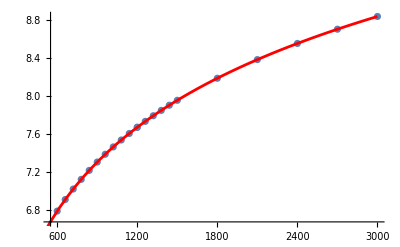

{b→-1.386855018887296908340676705438180334160379916194584349684432770263451755692543726671913832388369651,c→1.277532983826100336965475693130953645344761029923920550346329823641656674164940153499849819918124899}

```mathematica
Module[{table,fit,P1,P2,length},
length=Length[TestTableFull[[1,2]]];
table=Table[{elt[[1]],Log[elt[[2,length]]]},{elt,TestTableFull[[10;;]]}];
P1=ListPlot[table,PlotRange->All];
fit=FindFit[table,b+c*Log[L],{b,c},L];
P2=Plot[b+c*Log[L]/.fit,{L,0,3000},PlotStyle->Red];
Print[Show[P1,P2]];
Return[fit,Module];
]
```